```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Pri[ω_]:= tr[ω,0.0001,1,0]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
Clear[k31,k32,k33,k34,k35,k36,k37]
```

```mathematica
k31:=k31=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp3.dat"]][ω]},{ω,0,2,0.001}]
k32:=k32=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp3.dat"]][ω]},{ω,0,2,0.001}]
k33:=k33=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp3.dat"]][ω]},{ω,0,2,0.001}]
k34:=k34=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp3.dat"]][ω]},{ω,0,2,0.001}]
k35:=k35=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp3.dat"]][ω]},{ω,0,2,0.001}]
k36:=k36=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp3.dat"]][ω]},{ω,0,2,0.001}]
k37:=k37=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp3.dat"]][ω]},{ω,0,2,0.001}]
k41:=k41=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"]][ω]},{ω,0,2,0.001}]
k42:=k42=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp4.dat"]][ω]},{ω,0,2,0.001}]
k43:=k43=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"]][ω]},{ω,0,2,0.001}]
k44:=k44=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp4.dat"]][ω]},{ω,0,2,0.001}]
k45:=k45=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp4.dat"]][ω]},{ω,0,2,0.001}]
k46:=k46=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp4.dat"]][ω]},{ω,0,2,0.001}]
k47:=k47=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp4.dat"]][ω]},{ω,0,2,0.001}]
k51:=k51=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"]][ω]},{ω,0,2,0.001}]
k52:=k52=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp5.csv"]][ω]},{ω,0,2,0.001}]
k53:=k53=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"]][ω]},{ω,0,2,0.001}]
k54:=k54=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp5.csv"]][ω]},{ω,0,2,0.001}]
k55:=k55=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp5.csv"]][ω]},{ω,0,2,0.001}]
k56:=k56=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp5.csv"]][ω]},{ω,0,2,0.001}]
k57:=k57=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp5.csv"]][ω]},{ω,0,2,0.001}]
k61:=k61=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp6.dat"]][ω]},{ω,0,2,0.001}]
k62:=k62=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp6.dat"]][ω]},{ω,0,2,0.001}]
k63:=k63=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp6.dat"]][ω]},{ω,0,2,0.001}]
k64:=k64=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp6.dat"]][ω]},{ω,0,2,0.001}]
k65:=k65=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp6.dat"]][ω]},{ω,0,2,0.001}]
k66:=k66=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp6.dat"]][ω]},{ω,0,2,0.001}]
k67:=k67=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp6.dat"]][ω]},{ω,0,2,0.001}]
k71:=k71=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp7.dat"]][ω]},{ω,0,2,0.001}]
k72:=k72=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp7.dat"]][ω]},{ω,0,2,0.001}]
k73:=k73=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp7.dat"]][ω]},{ω,0,2,0.001}]
k74:=k74=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp7.dat"]][ω]},{ω,0,2,0.001}]
k75:=k75=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp7.dat"]][ω]},{ω,0,2,0.001}]
k76:=k76=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp7.dat"]][ω]},{ω,0,2,0.001}]
k77:=k77=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp7.dat"]][ω]},{ω,0,2,0.001}]
k81:=k81=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp8.dat"]][ω]},{ω,0,2,0.001}]
k82:=k82=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp8.dat"]][ω]},{ω,0,2,0.001}]
k83:=k83=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp8.dat"]][ω]},{ω,0,2,0.001}]
k84:=k84=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp8.dat"]][ω]},{ω,0,2,0.001}]
k85:=k85=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp8.dat"]][ω]},{ω,0,2,0.001}]
k86:=k86=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp8.dat"]][ω]},{ω,0,2,0.001}]
k87:=k87=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp8.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f3[ω_]:={{0,0.3,Pri[ω]},{1,0.3,k31[[ω*1000+1]][[2]]},{2,0.3,k32[[ω*1000+1]][[2]]},{3,0.3,k33[[ω*1000+1]][[2]]},{4,0.3,k34[[ω*1000+1]][[2]]},{5,0.3,k35[[ω*1000+1]][[2]]},{6,0.3,k36[[ω*1000+1]][[2]]},{7,0.3,k37[[ω*1000+1]][[2]]}}
f4[ω_]:={{0,0.4,Pri[ω]},{1,0.4,k41[[ω*1000+1]][[2]]},{2,0.4,k42[[ω*1000+1]][[2]]},{3,0.4,k43[[ω*1000+1]][[2]]},{4,0.4,k44[[ω*1000+1]][[2]]},{5,0.4,k45[[ω*1000+1]][[2]]},{6,0.4,k46[[ω*1000+1]][[2]]},{7,0.4,k47[[ω*1000+1]][[2]]}}
f5[ω_]:={{0,0.5,Pri[ω]},{1,0.5,k51[[ω*1000+1]][[2]]},{2,0.5,k52[[ω*1000+1]][[2]]},{3,0.5,k53[[ω*1000+1]][[2]]},{4,0.5,k54[[ω*1000+1]][[2]]},{5,0.5,k55[[ω*1000+1]][[2]]},{6,0.5,k56[[ω*1000+1]][[2]]},{7,0.5,k57[[ω*1000+1]][[2]]}}
f6[ω_]:={{0,0.6,Pri[ω]},{1,0.6,k61[[ω*1000+1]][[2]]},{2,0.6,k62[[ω*1000+1]][[2]]},{3,0.6,k63[[ω*1000+1]][[2]]},{4,0.6,k64[[ω*1000+1]][[2]]},{5,0.6,k65[[ω*1000+1]][[2]]},{6,0.6,k66[[ω*1000+1]][[2]]},{7,0.6,k67[[ω*1000+1]][[2]]}}
f7[ω_]:={{0,0.7,Pri[ω]},{1,0.7,k71[[ω*1000+1]][[2]]},{2,0.7,k72[[ω*1000+1]][[2]]},{3,0.7,k73[[ω*1000+1]][[2]]},{4,0.7,k74[[ω*1000+1]][[2]]},{5,0.7,k75[[ω*1000+1]][[2]]},{6,0.7,k76[[ω*1000+1]][[2]]},{7,0.7,k77[[ω*1000+1]][[2]]}}
f8[ω_]:={{0,0.8,Pri[ω]},{1,0.8,k81[[ω*1000+1]][[2]]},{2,0.8,k82[[ω*1000+1]][[2]]},{3,0.8,k83[[ω*1000+1]][[2]]},{4,0.8,k84[[ω*1000+1]][[2]]},{5,0.8,k85[[ω*1000+1]][[2]]},{6,0.8,k86[[ω*1000+1]][[2]]},{7,0.8,k87[[ω*1000+1]][[2]]}}
```

```mathematica
f[ω_]:=Join[f3[ω],f4[ω],f5[ω],f6[ω],f7[ω],f8[ω]]
```

```mathematica
ρ[ω_]:=Interpolation[f[ω]]
```

```mathematica
ρ[0.9]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

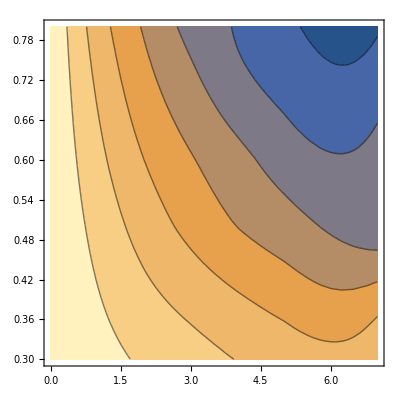

```mathematica
aa=ρ[0.8]
ContourPlot[aa[x,y],{x,0.,7.},{y,0.3,0.8}]
```

```mathematica
sl[ω_,n_,ϵ_]:=(ρ[ω][n,ϵ]-ρ[ω][n+.1,ϵ])/0.1+(ρ[ω][n,ϵ]-ρ[ω][n,ϵ+.1])/0.1+(ρ[ω][n,ϵ]-ρ[ω][n+0.1,ϵ+.1])/0.1
```

```mathematica
ρ[1]
```

InterpolatingFunction[…]

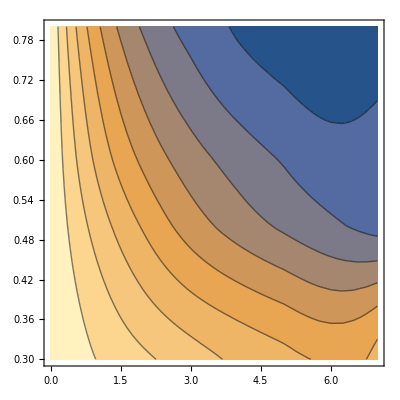

```mathematica
ContourPlot[%456[x,y],{x,0.,7.},{y,0.3,0.8}]
```

```mathematica
sl[1,.1,.3]
```

0.749082

```mathematica
Clear[meansl]
```

```mathematica
meansl[ω_,l_,p_]:=meansl[ω,l,p]=Mean[Flatten[Table[sl[ω,n,ϵ],{n,Range[0.1,l,0.1]},{ϵ,Range[0.3,p,0.1]}]]]
```

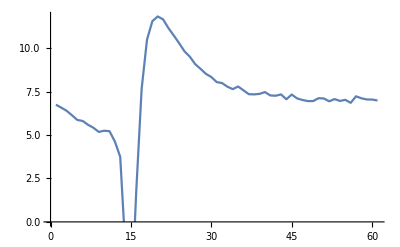

```mathematica
ListLinePlot[Table[meansl[ω,3,0.5],{ω,Range[0.9,1.5,0.01]}]]
```

```mathematica
Clear[a1,a2,a3,a4,a5,a6,a7]
```

```mathematica
a1:=a1=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp3.dat"]][ω]},{ω,0,2,0.001}]
a2:=a2=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"]][ω]},{ω,0,2,0.001}]
a3:=a3=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"]][ω]},{ω,0,2,0.001}]
a4:=a4=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp6.dat"]][ω]},{ω,0,2,0.001}]
a5:=a5=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp7.dat"]][ω]},{ω,0,2,0.001}]
a6:=a6=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp8.dat"]][ω]},{ω,0,2,0.001}]
a7:=a7=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp9.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
g5[ω_]:={{0,Pri[ω]},{0.3,a1[[ω*1000+1]][[2]]},{0.4,a2[[ω*1000+1]][[2]]},{0.5,a3[[ω*1000+1]][[2]]},{0.6,a4[[ω*1000+1]][[2]]},{0.7,a5[[ω*1000+1]][[2]]},{0.8,a6[[ω*1000+1]][[2]]},{0.9,a7[[ω*1000+1]][[2]]}}
```

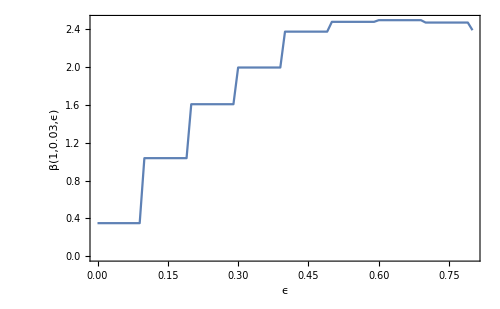

```mathematica
Show[%325,FrameLabel->{{HoldForm[β[1,0.03,ϵ]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
φ3[ω_]:=Interpolation[f3[ω]]
sloap3[ω_,n_]:=(φ3[ω][n]-φ3[ω][n+.1])/0.1
s3[ω_,l_]:=s3[ω,l]=Mean[Table[sloap3[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ4[ω_]:=Interpolation[f4[ω]]
sloap4[ω_,n_]:=(φ4[ω][n]-φ4[ω][n+.1])/0.1
s4[ω_,l_]:=s4[ω,l]=Mean[Table[sloap4[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ5[ω_]:=Interpolation[f5[ω]]
sloap5[ω_,n_]:=(φ5[ω][n]-φ5[ω][n+.1])/0.1
s5[ω_,l_]:=s5[ω,l]=Mean[Table[sloap5[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ6[ω_]:=Interpolation[f6[ω]]
sloap6[ω_,n_]:=(φ6[ω][n]-φ6[ω][n+.1])/0.1
s6[ω_,l_]:=s6[ω,l]=Mean[Table[sloap6[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ7[ω_]:=Interpolation[f7[ω]]
sloap7[ω_,n_]:=(φ7[ω][n]-φ7[ω][n+.1])/0.1
s7[ω_,l_]:=s7[ω,l]=Mean[Table[sloap7[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ8[ω_]:=Interpolation[f8[ω]]
sloap8[ω_,n_]:=(φ8[ω][n]-φ8[ω][n+.1])/0.1
s8[ω_,l_]:=s8[ω,l]=Mean[Table[sloap8[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],Table[imp,58]]]
```

{imp2,imp,imp12,imp11,imp12,imp5,imp,imp13,imp,imp,imp,imp,imp4,imp11,imp,imp1,imp4,imp,imp,imp,imp1,imp,imp,imp,imp3,imp,imp,imp,imp6,imp3,imp8,imp10,imp,imp7,imp7,imp,imp10,imp,imp6,imp14,imp,imp,imp,imp9,imp,imp,imp5,imp4,imp9,imp13,imp,imp7,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp2,imp,imp2,imp14,imp,imp5,imp8,imp,imp11,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp10,imp6,imp,imp,imp,imp12,imp,imp13,imp,imp,imp3,imp,imp14,imp,imp,imp,imp}

```mathematica
μ1=RandomInteger[{1,14}]; μ2=RandomInteger[{1,14}]; μ3=RandomInteger[{1,14}]; μ4=RandomInteger[{1,14}];μ5=RandomInteger[{1,14}]; μ6=RandomInteger[{1,14}]; μ7=RandomInteger[{1,14}];μ8=RandomInteger[{1,14}]; μ9=RandomInteger[{1,14}]; μ10=RandomInteger[{1,14}]; μ11=RandomInteger[{1,14}];μ12=RandomInteger[{1,14}]; μ13=RandomInteger[{1,14}]; μ14=RandomInteger[{1,14}]
m5[ϵ1_,l_,p_,lim1_,lim2_]:=Module[{Tin=T1[1],T=TT[1](*,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]*)},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp2,imp,imp12,imp11,imp12,imp5,imp,imp13,imp,imp,imp,imp,imp4,imp11,imp,imp1,imp4,imp,imp,imp,imp1,imp,imp,imp,imp3,imp,imp,imp,imp6,imp3,imp8,imp10,imp,imp7,imp7,imp,imp10,imp,imp6,imp14,imp,imp,imp,imp9,imp,imp,imp5,imp4,imp9,imp13,imp,imp7,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp2,imp,imp2,imp14,imp,imp5,imp8,imp,imp11,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp10,imp6,imp,imp,imp,imp12,imp,imp13,imp,imp,imp3,imp,imp14,imp,imp,imp,imp}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
mm=Table[{ω,tra1},{ω,Range[0,2,0.01]}];
m=Table[{ω,Interpolation[mm][ω]},{ω,0,2,0.001}];v1=Module[{},(*ρ3=NIntegrate[Interpolation[Table[{ω,s3[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s3[ω,k]*s3[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);
ρ4=NIntegrate[Interpolation[Table[{ω,s4[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s4[ω,k]*s4[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);ρ5=NIntegrate[Interpolation[Table[{ω,s5[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s5[ω,k]*s5[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);
ρ6=NIntegrate[Interpolation[Table[{ω,s6[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s6[ω,k]*s6[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);ρ7=NIntegrate[Interpolation[Table[{ω,s7[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s7[ω,k]*s7[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);ρ8=NIntegrate[Interpolation[Table[{ω,s8[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s8[ω,k]*s8[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);
*)ρ9=NIntegrate[Interpolation[Table[{ω,(Pri[ω]-m[[ω*1000+1]][[2]])^2},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]-NIntegrate[Interpolation[Table[{ω,meansl[ω,l,p]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]^2/(NIntegrate[Interpolation[Table[{ω,(meansl[ω,l,p]*meansl[ω,l,p])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]);{(*{0.3,Abs[ρ3]},{0.4,Abs[ρ4]},{0.5,Abs[ρ5]},{0.6,Abs[ρ6]},{0.7,Abs[ρ7]},{0.8,Abs[ρ8]},*)ρ9}];v1]
```

10

```mathematica
Table[{k,m5[0.5,k,0.3,0.9,1.5][[1]]},{k,Range[1,6,1]}]
```

{{1,0.918724},{2,0.76633},{3,0.610273},{4,0.517856},{5,0.462512},{6,0.427186}}

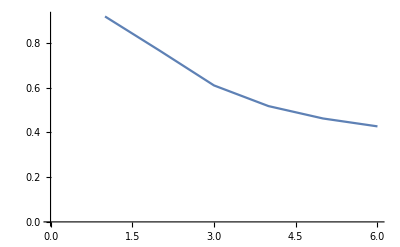

```mathematica
ListPlot[{{1,0.9187244082898731},{2,0.7663303821181833},{3,0.6102725066304764},{4,0.5178557360433835},{5,0.46251174620846536},{6,0.42718618209715586}},Joined->True]
```

```mathematica
Table[{k,m5[0.5,k,0.4,0.9,1.5][[1]]},{k,Range[1,6,1]}]
```

{{1,0.595899},{2,0.537616},{3,0.462294},{4,0.419714},{5,0.396509},{6,0.386066}}

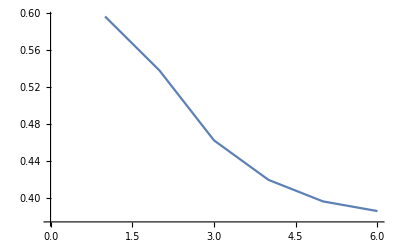

```mathematica
ListPlot[{{1,0.5958988852884946},{2,0.5376161804954864},{3,0.4622940172405947},{4,0.4197138473182571},{5,0.3965093570598177},{6,0.38606638838066365}},Joined->True]
```

```mathematica
Table[{k,m5[0.5,k,0.6,0.9,1.5][[1]]},{k,Range[1,6,1]}]
```

{{1,0.336964},{2,0.361872},{3,0.360784},{4,0.363915},{5,0.370342},{6,0.378928}}

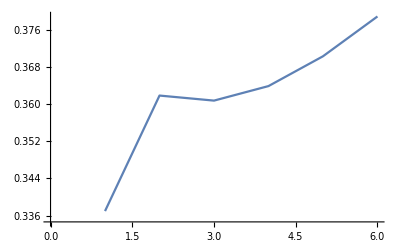

```mathematica
ListPlot[{{1,0.33696424431497984},{2,0.3618723917059543},{3,0.36078366735361556},{4,0.36391547617697384},{5,0.3703418528289584},{6,0.37892778351588596}},Joined->True]
```

```mathematica
Table[{k,m5[0.5,k,0.7,0.9,1.5][[1]]},{k,Range[1,6,1]}]
```

{{1,0.291872},{2,0.32866},{3,0.338992},{4,0.348944},{5,0.359971},{6,0.371989}}

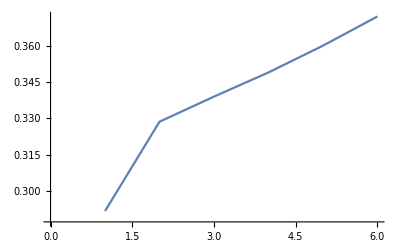

```mathematica
ListPlot[{{1,0.29187197824886324},{2,0.3286603955464775},{3,0.3389922787621775},{4,0.34894398735712384},{5,0.35997107003924533},{6,0.3719886097931271}},Joined->True]
```

```mathematica
Table[{k,m5[0.5,k,0.8,0.9,1.5][[1]]},{k,Range[1,6,1]}]
```

{{1,0.268486},{2,0.310784},{3,0.324145},{4,0.33532},{5,0.348933},{6,0.363186}}

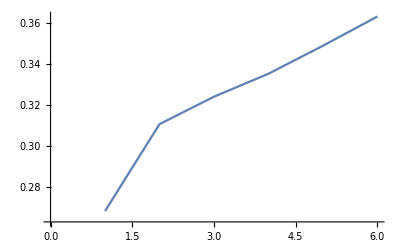

```mathematica
ListPlot[{{1,0.2684856055694844},{2,0.3107840583530974},{3,0.32414543110488925},{4,0.3353198465500875},{5,0.3489327825362669},{6,0.3631857534480578}},Joined->True]
```

```mathematica
Table[{k,m5[0.5,k,0.5,0.9,1.5][[1]]},{k,Range[1,6,1]}]
```

{{1,0.291854},{2,0.288092},{3,0.268774},{4,0.261649},{5,0.26254},{6,0.267378}}

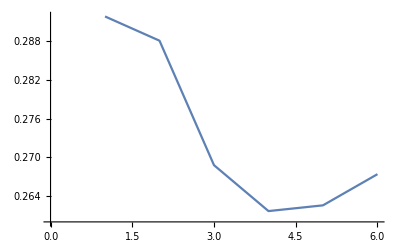

```mathematica
ListPlot[{{1,0.29185421186071503},{2,0.28809230591166335},{3,0.26877395771452006},{4,0.261649147305695},{5,0.26254015256959384},{6,0.26737798103973187}},Joined->True]
```

```mathematica
Join[%542,%543,%544,%545,%546]
```

{{1,0.918724},{2,0.76633},{3,0.610273},{4,0.517856},{5,0.462512},{6,0.427186},{1,0.595899},{2,0.537616},{3,0.462294},{4,0.419714},{5,0.396509},{6,0.386066},{1,0.336964},{2,0.361872},{3,0.360784},{4,0.363915},{5,0.370342},{6,0.378928},{1,0.291872},{2,0.32866},{3,0.338992},{4,0.348944},{5,0.359971},{6,0.371989},{1,0.268486},{2,0.310784},{3,0.324145},{4,0.33532},{5,0.348933},{6,0.363186}}

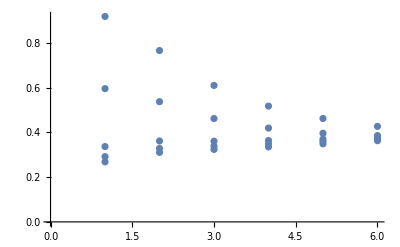

```mathematica
ListPlot[%547]
```

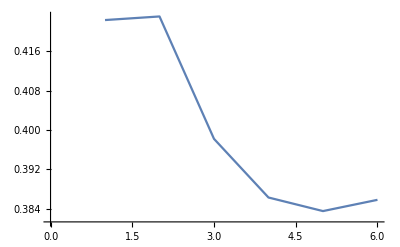

```mathematica
ListPlot[{{1,0.42236071185187685},{2,0.4230921925026565},{3,0.3982139055903655},{4,0.38629359878773917},{5,0.38353435919517764},{6,0.38582123452352723}},Joined->True]
```

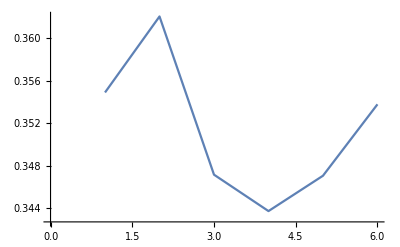

```mathematica
ListPlot[{{1,0.3548899545820743},{2,0.3620530917906377},{3,0.3471420866448218},{4,0.3437101002925065},{5,0.34704161652522103},{6,0.3537724475611359}},Joined->True]
```

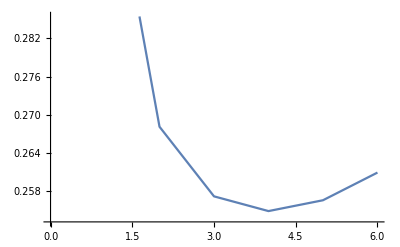

```mathematica
ListPlot[{{1,0.31514682536766486},{2,0.2681227825330073},{3,0.2572052122491632},{4,0.25489467390103826},{5,0.25659375331211864},{6,0.26093369949427386}},Joined->True]
```

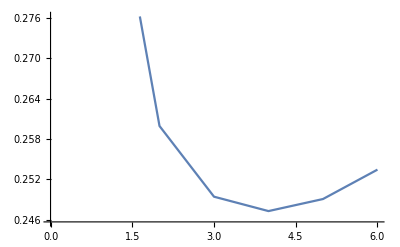

```mathematica
ListPlot[{{1,0.3050259012117767},{2,0.259939848355765},{3,0.2494395866357362},{4,0.2473010610209118},{5,0.2490910981640409},{6,0.2534590739497396}},Joined->True]
```

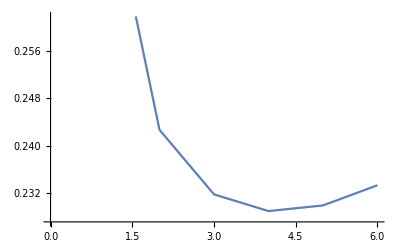

```mathematica
ListPlot[{{1,0.28677001899033894},{2,0.2426730092530147},{3,0.23177578979158145},{4,0.22895032859217945},{5,0.2299049492908048},{6,0.23331304010530965}},Joined->True]
```

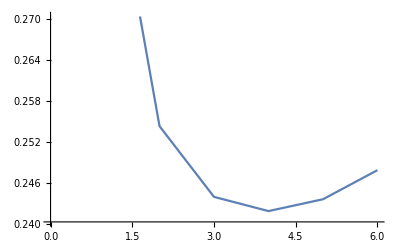

```mathematica
ListPlot[{{1,0.2992472288179464},{2,0.25433595956009364},{3,0.24396934732559922},{4,0.24188795158625628},{5,0.24362185292509053},{6,0.24788486721327457}},Joined->True]
```

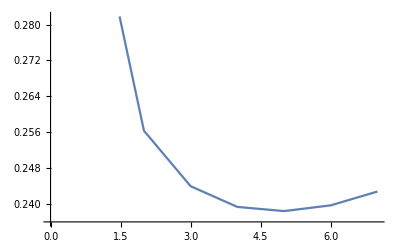

```mathematica
ListPlot[{{1,0.30518324535498176},{2,0.2562774630032646},{3,0.24388476134442386},{4,0.23925893913541962},{5,0.23832839406844653},{6,0.23960797497524702},{7,0.2426988361059029}},Joined->True]
```

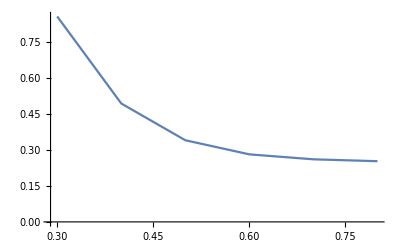

```mathematica
ListPlot[{{0.3,0.8546522215728114},{0.4,0.49263887111968163},{0.5,0.33966615276211254},{0.6000000000000001,0.2809441688415788},{0.7,0.2603588953014597},{0.8,0.2524956194955186}},Joined->True]
```

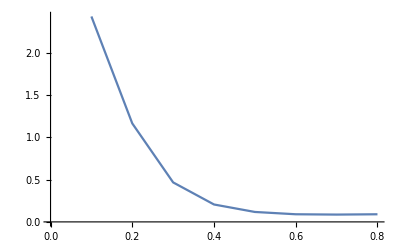

```mathematica
ListPlot[%321,Joined->True]
```

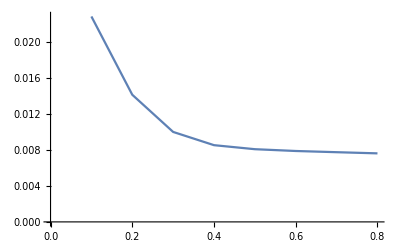

```mathematica
ListPlot[%319,Joined->True]
```

```mathematica
%314
```

```mathematica
{{0.1,0.6071679590143242},{0.2,0.20949021064096707},{0.30000000000000004,0.07223597168798146},{0.4,0.05868556416961068},{0.5,0.07086555689640384},{0.6,0.0839581368774398`+0.01},{0.7000000000000001,0.09418856211087179`+0.015},{0.8,0.10014184105975388`+0.02}}
```

{{0.1,0.607168},{0.2,0.20949},{0.3,0.072236},{0.4,0.0586856},{0.5,0.0708656},{0.6,0.08},{0.7,0.09},{0.8,0.1}}

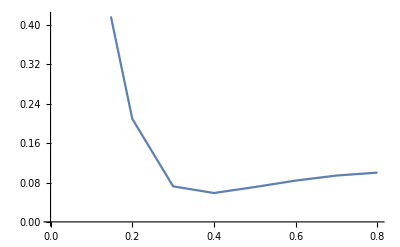

```mathematica
ListPlot[%329,Joined->True]
```

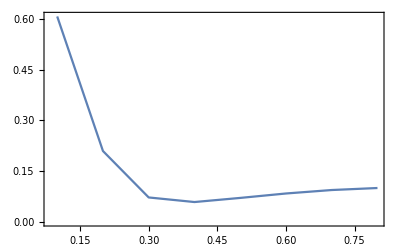

```mathematica
ListPlot[%329,Joined->True,PlotRange->All,Frame->True]
```

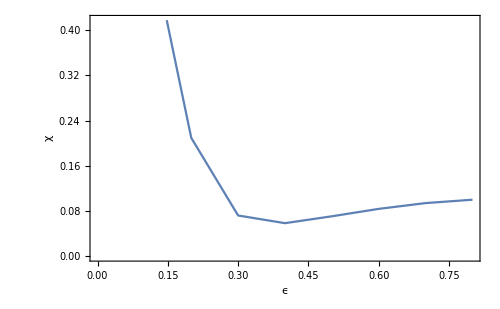

```mathematica
Show[%330,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{18,GrayLevel[0]},ImageSize->{500,500}]
```

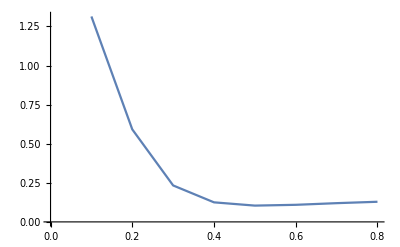

```mathematica
ListPlot[%260,Joined->True]
```

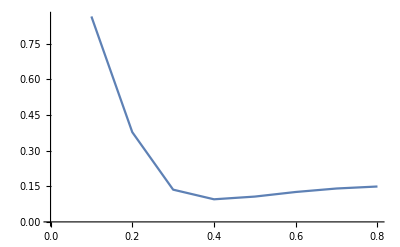

```mathematica
ListPlot[%255,Joined->True]
```

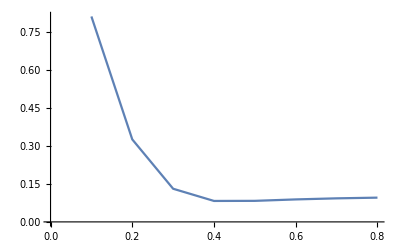

```mathematica
ListPlot[%251,Joined->True]
```

```mathematica
aa=Table[m5[0.5,k],{k,5}]
```

{{{0.3,2.90405},{0.4,2.17218},{0.5,1.72114},{0.6,1.43778},{0.7,1.25087},{0.8,1.12504}},{{0.3,4.17284},{0.4,3.08913},{0.5,2.47224},{0.6,2.13887},{0.7,1.92744},{0.8,1.79879}},{{0.3,5.11487},{0.4,3.83502},{0.5,3.13292},{0.6,2.79819},{0.7,2.59572},{0.8,2.48487}},{{0.3,5.94694},{0.4,4.53604},{0.5,3.78126},{0.6,3.46423},{0.7,3.28236},{0.8,3.19834}},{{0.3,6.70713},{0.4,5.20498},{0.5,4.42354},{0.6,4.1464},{0.7,3.99503},{0.8,3.93769}}}

```mathematica
Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]]]
```

{{0.3,2.90405},{0.4,2.17218},{0.5,1.72114},{0.6,1.43778},{0.7,1.25087},{0.8,1.12504},{0.3,4.17284},{0.4,3.08913},{0.5,2.47224},{0.6,2.13887},{0.7,1.92744},{0.8,1.79879},{0.3,5.11487},{0.4,3.83502},{0.5,3.13292},{0.6,2.79819},{0.7,2.59572},{0.8,2.48487},{0.3,5.94694},{0.4,4.53604},{0.5,3.78126},{0.6,3.46423},{0.7,3.28236},{0.8,3.19834},{0.3,6.70713},{0.4,5.20498},{0.5,4.42354},{0.6,4.1464},{0.7,3.99503},{0.8,3.93769}}

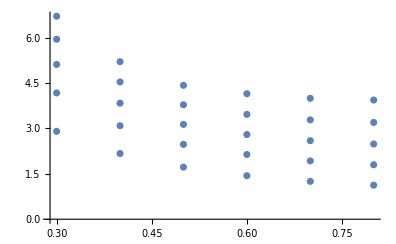

```mathematica
ListPlot[%104]
```

```mathematica
Min[aa]
```

-4.1341

```mathematica
Interpolation[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]]]]
```

InterpolatingFunction[…]

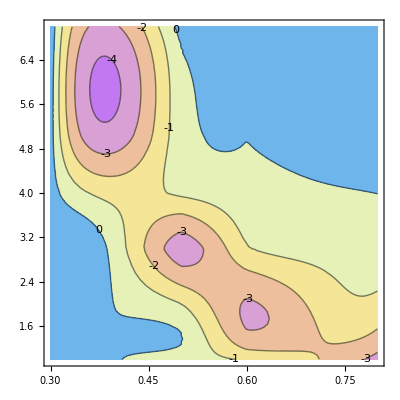

```mathematica
ap=ContourPlot[%88[x,y],{x,0.3,0.8},{y,1.,7.},ColorFunction->"Pastel",ContourLabels->True,Frame->True,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Axes->False]
```

```mathematica
Interpolation[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]]]]
```

InterpolatingFunction[…]

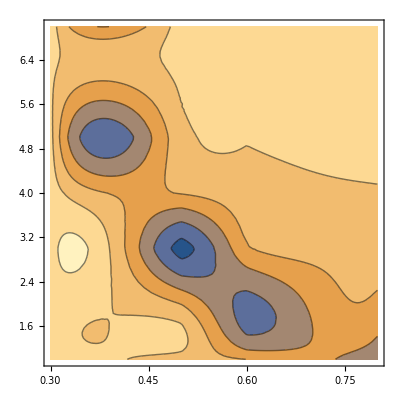

```mathematica
ContourPlot[%174[x,y],{x,0.3,0.8},{y,1.,7.},Frame->True,ImagePadding->{{Automatic, 10}, {Automatic, 10}}]
```

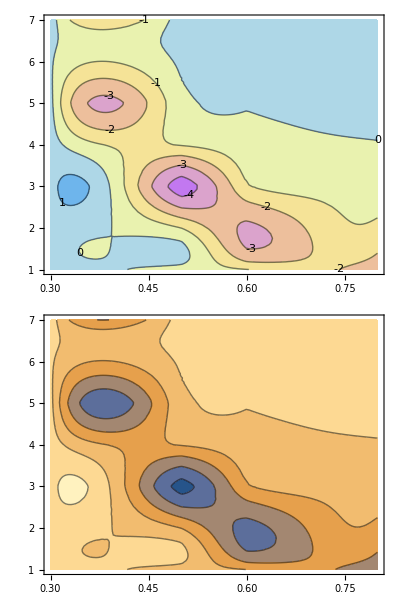

```mathematica
Column[{%196,%197},Spacings->0]
```

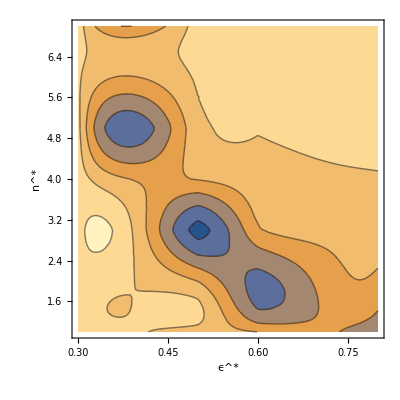

```mathematica
Show[%176,FrameLabel->{{HoldForm[SuperStar[n]],None},{HoldForm[SuperStar[ϵ]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

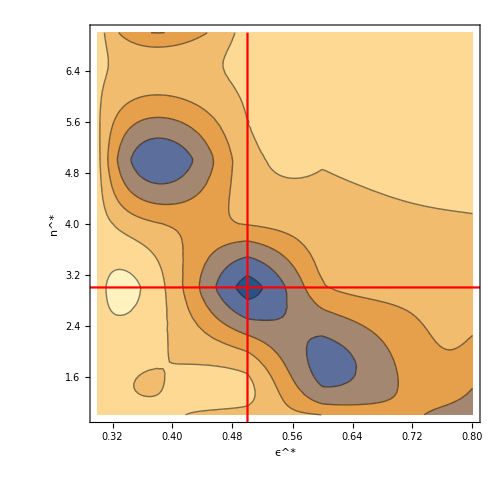

```mathematica
Show[%191,ListLinePlot[{Table[{0.5,y},{y,Range[0,7.5,0.075]}],Table[{y,3},{y,Range[0,4,0.075]}]},PlotStyle->{{Dashing[{0.01,0.01,1*^-2,1*^-2}],Red},{Dashing[{1*^-2,0.01,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}},Frame->True]]
```

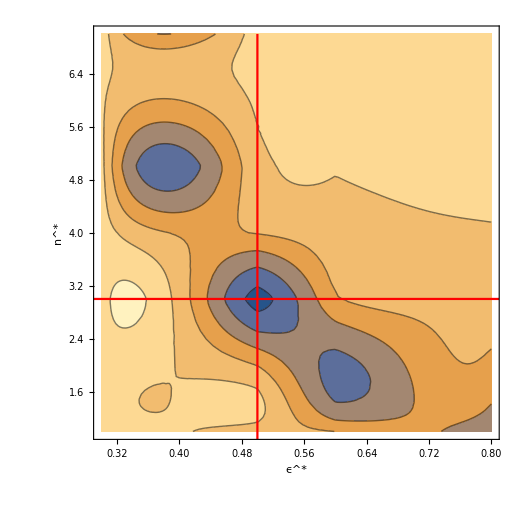

```mathematica
Show[%193,ImageSize->{520,520}]
```

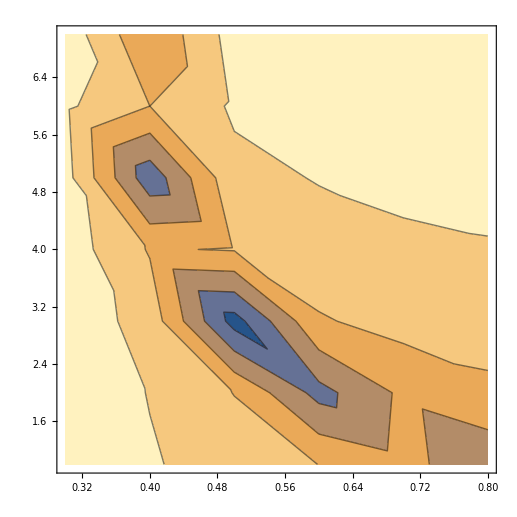

```mathematica
ListContourPlot[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]]]]
```

```mathematica
Min[%164]
```

0.0120911

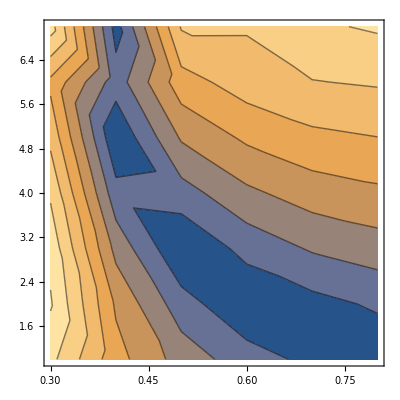

```mathematica
ListContourPlot[%164]
```

```mathematica
Join[%152[[3]]]
```

{{0.3,3,4.77477},{0.4,3,3.578},{0.5,3,2.91032},{0.6,3,2.59379},{0.7,3,2.39922},{0.8,3,2.29126}}

```mathematica
misfinew[0,1.5][[1]]
```

{{2,0.00179114},{3,0.00145881},{4,0.00116216},{5,0.000924725},{6,0.000701735},{7,0.000536314},{8,0.000403517},{9,0.000329386},{10,0.000312483},{11,0.000285121}}

```mathematica
misfinew[0,1.5][[2]]
```

{{2,0.00091239},{3,0.00149644},{4,0.00251629},{5,0.00373068},{6,0.00512921},{7,0.00656333},{8,0.00804064},{9,0.0100383},{10,0.0107704},{11,0.0121276}}

```mathematica
misfinew[0,1.5][[3]]
```

{{2,0.000833579},{3,0.000432331},{4,0.000255224},{5,0.000227191},{6,0.000336408},{7,0.000575701},{8,0.000873683},{9,0.00131699},{10,0.00154469},{11,0.00196306}}

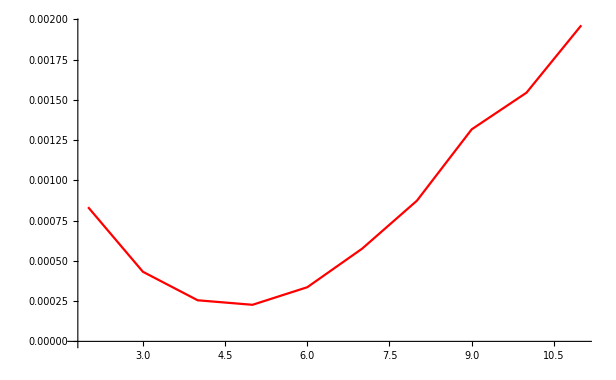

```mathematica
ListPlot[%723,Joined->True,PlotStyle->Red]
```

```mathematica
misfinew[0,1.5][[4]]
```

{{2,0.000632291},{3,0.000596905},{4,0.000923073},{5,0.00148581},{6,0.00222982},{7,0.00309602},{8,0.00401582},{9,0.00525917},{10,0.00576541},{11,0.00671158}}

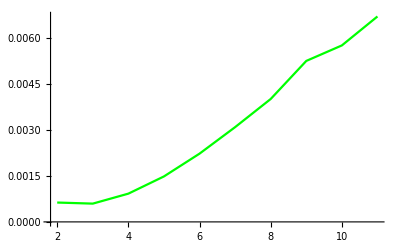

```mathematica
ListPlot[%724,Joined->True,PlotStyle->Green]
```

```mathematica
ListPlot[%721,Joined->True,PlotStyle->Blue]
```

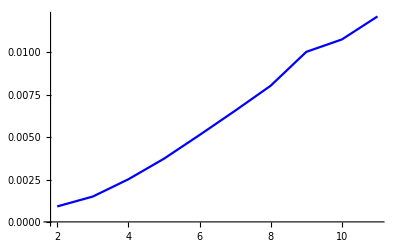

-Graphics-

```mathematica
ListPlot[%719,Joined->True,PlotStyle->Gray]
```

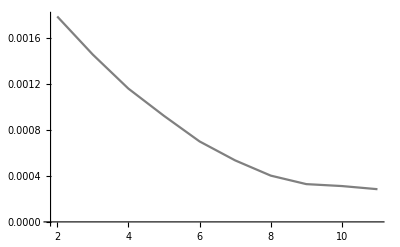

-Graphics-

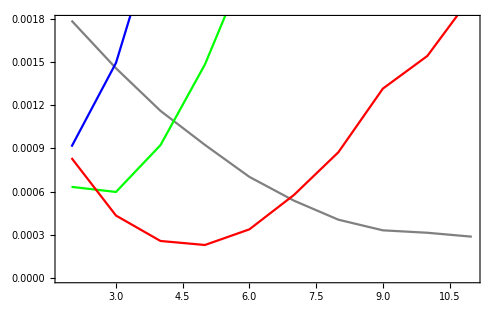

```mathematica
Show[%730,%729,%728,%727,ImageSize->{500,500},Frame->True]
```

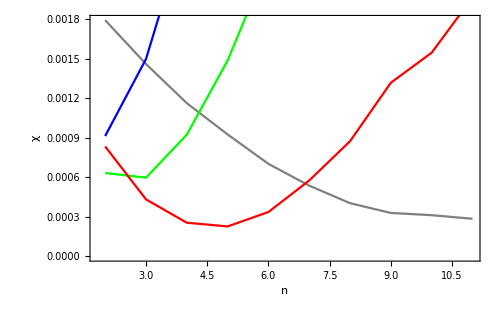

```mathematica
Show[%733,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],RawBoxes[RowBox[{RowBox[{"Blue","="," ","0.9"}]," ",","," ",RowBox[{"Gray","=","0.3"}],","," ",RowBox[{"Green"," ","="," ","0.7"}]}]]}},PlotLabel->None,LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
misfinew[y_,x_]:= Module[{},
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list1:={{2,-Log[ρ2]^2},{3,-Log[ρ3]^2},{4,-Log[ρ4]^2},{5,-Log[ρ5]^2},{6,-Log[ρ6]^2},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11}};
{{0.3,2,-Log[ρ2]^2},{0.3,3,-Log[ρ3]^2},{0.3,4,-Log[ρ4]^2},{0.3,5,-Log[ρ5]^2},{0.3,6,-Log[ρ6]^2},{0.3,7,ρ7},{0.3,8,ρ8},{0.3,9,ρ9},{0.3,10,ρ10},{0.3,11,ρ11}}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp4.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list1:={{2,-Log[ρ2]^2},{3,-Log[ρ3]^2},{4,-Log[ρ4]^2},{5,-Log[ρ5]^2},{6,-Log[ρ6]^2},{7,ρ7},{8,ρ8}(*,{9,ρ9},{10,ρ10},{11,ρ11}*)};
{{0.4,2,-Log[ρ2]^2},{0.4,3,-Log[ρ3]^2},{0.4,4,-Log[ρ4]^2},{0.4,5,-Log[ρ5]^2},{0.4,6,-Log[ρ6]^2},{0.4,7,ρ7},{0.4,8,ρ8}(*,{9,ρ9},{10,ρ10},{11,ρ11}*)}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
{{0.5,2,-Log[ρ2]^2},{0.5,3,-Log[ρ3]^2},{0.5,4,-Log[ρ4]^2},{0.5,5,-Log[ρ5]^2},{0.5,6,-Log[ρ6]^2},{0.5,7,ρ7},{0.5,8,ρ8},{0.5,9,ρ9},{0.5,10,ρ10},{0.5,11,ρ11}}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp6.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];(*ρ9:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp5.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];*)
{{0.6,2,-Log[ρ2]^2},{0.6,3,-Log[ρ3]^2},{0.6,4,-Log[ρ4]^2},{0.6,5,-Log[ρ5]^2},{0.6,6,-Log[ρ6]^2},{0.6,7,ρ7},{0.6,8,ρ8}(*,{9,ρ9},{10,ρ10},{11,ρ11}*)}];
υ5=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
{{0.7,2,-Log[ρ2]^2},{0.7,3,-Log[ρ3]^2},{0.7,4,-Log[ρ4]^2},{0.7,5,-Log[ρ5]^2},{0.7,6,-Log[ρ6]^2},{0.7,7,ρ7},{0.7,8,ρ8},{0.7,9,ρ9},{0.7,10,ρ10},{0.7,11,ρ11}}];
υ6=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp8.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];(*ρ9:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];*)
{{0.8,2,-Log[ρ2]^2},{0.8,3,-Log[ρ3]^2},{0.8,4,-Log[ρ4]^2},{0.8,5,-Log[ρ5]^2},{0.8,6,-Log[ρ6]^2},{0.8,7,ρ7},{0.8,8,ρ8},{0.8,9,ρ9},{0.8,10,ρ10},{0.8,11,ρ11}}];
υ7=Module[{},
ρ2:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%70[[1;;400]][[;;,1]],(%70[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp9.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
{{0.9,2,-Log[ρ2]^2},{0.9,3,-Log[ρ3]^2},{0.9,4,-Log[ρ4]^2},{0.9,5,-Log[ρ5]^2},{0.9,6,-Log[ρ6]^2},{0.9,7,ρ7},{0.9,8,ρ8},{0.9,9,ρ9},{0.9,10,ρ10},{0.9,11,ρ11}}];
{υ1,υ2,υ3,υ4,υ5,υ6,υ7}]
```

```mathematica
misfinew[0,1.5]
```

{{{0.3,2,0.00371828},{0.3,3,0.00302571},{0.3,4,0.00229667},{0.3,5,0.00177098},{0.3,6,0.00122123},{0.3,7,0.000894532},{0.3,8,0.000633102},{0.3,9,0.000478752},{0.3,10,0.000372595},{0.3,11,0.000283064}},{{0.4,2,0.00239668},{0.4,3,0.00159624},{0.4,4,0.000976047},{0.4,5,0.000613081},{0.4,6,0.000342364},{0.4,7,0.000213659},{0.4,8,0.000166986}},{{0.5,2,0.00114126},{0.5,3,0.000515793},{0.5,4,0.000226004},{0.5,5,0.0000961204},{0.5,6,0.000057459},{0.5,7,0.0000666308},{0.5,8,0.000110722},{0.5,9,0.000227927},{0.5,10,0.000291471},{0.5,11,0.000451216}},{{0.6,2,0.0005105},{0.6,3,0.000133849},{0.6,4,0.000037063},{0.6,5,0.0000288157},{0.6,6,0.0000831193},{0.6,7,0.00020601},{0.6,8,0.000420127}},{{0.7,2,0.000361205},{0.7,3,0.000084692},{0.7,4,0.0000508481},{0.7,5,0.000122831},{0.7,6,0.000365812},{0.7,7,0.000825786},{0.7,8,0.00150914},{0.7,9,0.00284483},{0.7,10,0.00360133},{0.7,11,0.00499175}},{{0.8,2,0.000389094},{0.8,3,0.00013404},{0.8,4,0.000174146},{0.8,5,0.000461622},{0.8,6,0.00116577},{0.8,7,0.00230526},{0.8,8,0.00381708},{0.8,9,0.00284483},{0.8,10,0.00360133},{0.8,11,0.00499175}},{{0.9,2,0.000458417},{0.9,3,0.000236403},{0.9,4,0.000509342},{0.9,5,0.00122975},{0.9,6,0.00267593},{0.9,7,0.00463897},{0.9,8,0.00731869},{0.9,9,0.0117751},{0.9,10,0.0135766},{0.9,11,0.0173671}}}

{{5.,2,0.00114126},{5.,3,0.000515793},{5.,4,0.000226004},{5.,5,0.0000961204},{5.,6,0.000057459},{5.,7,0.0000666308},{5.,8,0.000110722},{6.,2,0.0005105},{6.,3,0.000133849},{6.,4,0.000037063},{6.,5,0.0000288157},{6.,6,0.0000831193},{6.,7,0.00020601},{6.,8,0.000420127},{7.,2,0.000361205},{7.,3,0.000084692},{7.,4,0.0000508481},{7.,5,0.000122831},{7.,6,0.000365812},{7.,7,0.000825786},{7.,8,0.00150914}}

```mathematica
Transpose[%175]
```

{{5.,5.,5.,5.,5.,5.,5.,6.,6.,6.,6.,6.,6.,6.,7.,7.,7.,7.,7.,7.,7.},{2,3,4,5,6,7,8,2,3,4,5,6,7,8,2,3,4,5,6,7,8},{0.00114126,0.000515793,0.000226004,0.0000961204,0.000057459,0.0000666308,0.000110722,0.0005105,0.000133849,0.000037063,0.0000288157,0.0000831193,0.00020601,0.000420127,0.000361205,0.000084692,0.0000508481,0.000122831,0.000365812,0.000825786,0.00150914}}

```mathematica
Transpose[{%178[[1]]/10,%178[[2]],Log[%178[[3]]]}]
```

{{0.5,2,-6.77562},{0.5,3,-7.5698},{0.5,4,-8.39496},{0.5,5,-9.24991},{0.5,6,-9.76444},{0.5,7,-9.61634},{0.5,8,-9.10849},{0.6,2,-7.58012},{0.6,3,-8.91879},{0.6,4,-10.2029},{0.6,5,-10.4546},{0.6,6,-9.39523},{0.6,7,-8.48758},{0.6,8,-7.77495},{0.7,2,-7.92606},{0.7,3,-9.37649},{0.7,4,-9.88667},{0.7,5,-9.0047},{0.7,6,-7.91339},{0.7,7,-7.09918},{0.7,8,-6.49622}}

```mathematica
ListPlot3D[%188]
```

-Graphics3D-

```mathematica
ListPlot3D[%188,PlotStyle->Directive[RGBColor[0.26,1.,0.36],Opacity[1.]]]
```

-Graphics3D-

```mathematica
ListPlot3D[%188,Mesh->Automatic,MeshFunctions->{#3&},PlotStyle->Directive[RGBColor[0.26,1.,0.36],Opacity[1.]]]
```

-Graphics3D-

```mathematica
Show[%194,Boxed->False]
```

-Graphics3D-

```mathematica
Show[%195,ViewPoint->{∞,0,0},AxisLable->{ϵ,n,Log[χ]}]
```

-Graphics3D-

```mathematica
Interpolation[Transpose[Join[{%162[[1]]*10},{%162[[2]]},{%162[[3]]}]]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[…]

```mathematica
Interpolation[%188]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2,3}.

InterpolatingFunction[…]

```mathematica
Plot3D[%190[x,y],{x,0.5,0.7},{y,2.,8.}]
```

-Graphics3D-

```mathematica
Plot3D[%190[x,y],{x,0.5,0.7},{y,2.,8.},PlotStyle->RGBColor[0.21,1.,0.48]]
```

-Graphics3D-

```mathematica
Plot3D[%190[x,y],{x,0.5,0.7},{y,2.,8.},Mesh->Automatic,MeshFunctions->{#3&},PlotStyle->RGBColor[0.21,1.,0.48]]
```

-Graphics3D-

```mathematica
%190
```

InterpolatingFunction[…]

```mathematica
Plot3D[%404[x,y],{x,0.5,0.7000000000000001},{y,2.,8.}]
```

-Graphics3D-

```mathematica
Plot3D[%190[x,y]^15,{x,0.5,0.7},{y,2.,8.},PlotTheme->"Scientific",Mesh->Automatic,MeshFunctions->{#3&},PlotStyle->RGBColor[0.21,1.,0.48],AxesLabel->{ϵ,n,Log[χ]},LabelStyle->{16,GrayLevel[0]},ImageSize->{500,500}]
```

-Graphics3D-

```mathematica
Show[%206,Axes->False]
```

-Graphics3D-

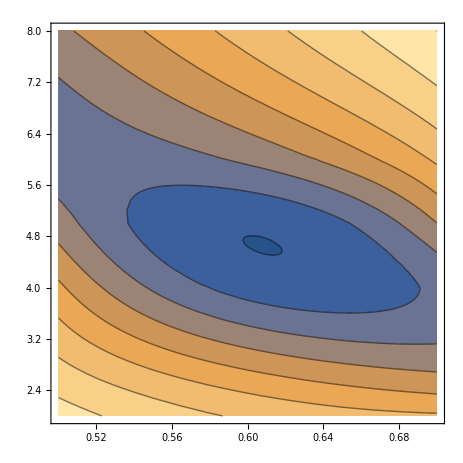

```mathematica
ContourPlot[%190[x,y],{x,0.5,0.7},{y,2.,8.},ImageSize->{500,500}]
```

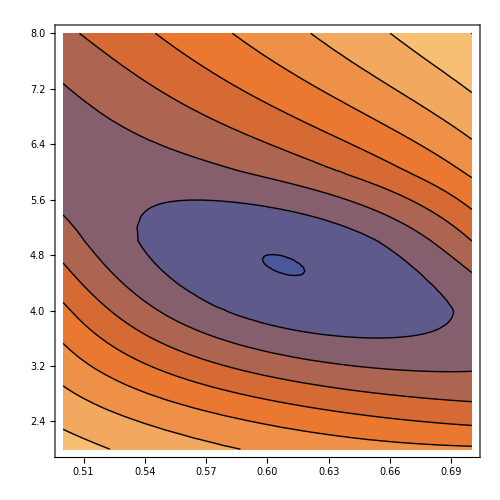

```mathematica
ContourPlot[%190[x,y],{x,0.5,0.7},{y,2.,8.},PlotTheme->"Scientific",ImageSize->{500,500}]
```

```mathematica
Table[{x,4.75},{x,Range[0.5,0.61,0.01]}]
```

{{0.5,4.75},{0.51,4.75},{0.52,4.75},{0.53,4.75},{0.54,4.75},{0.55,4.75},{0.56,4.75},{0.57,4.75},{0.58,4.75},{0.59,4.75},{0.6,4.75},{0.61,4.75}}

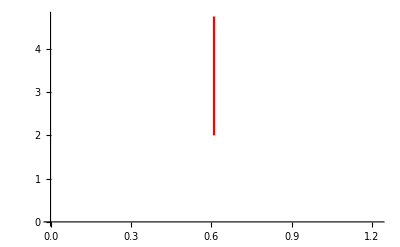

```mathematica
ListLinePlot[Table[{0.61,x},{x,Range[2,4.75,0.01]}],PlotStyle->Red]
```

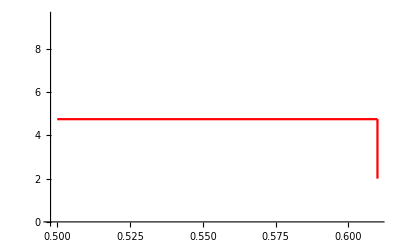

```mathematica
Show[ListLinePlot[%259,PlotStyle->Red],%252]
```

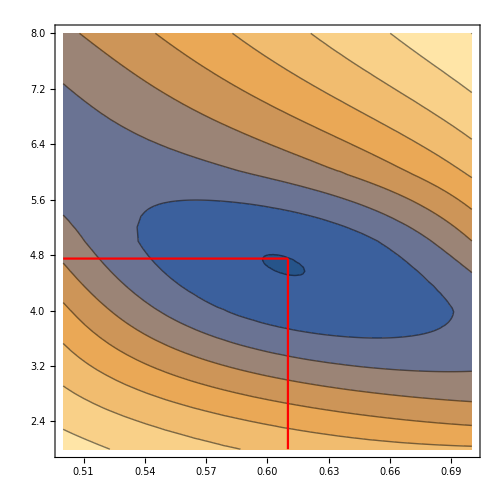

```mathematica
Show[%207,%260]
```

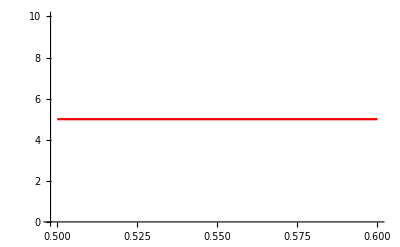

```mathematica
ListLinePlot[%224,PlotStyle->Red]
```

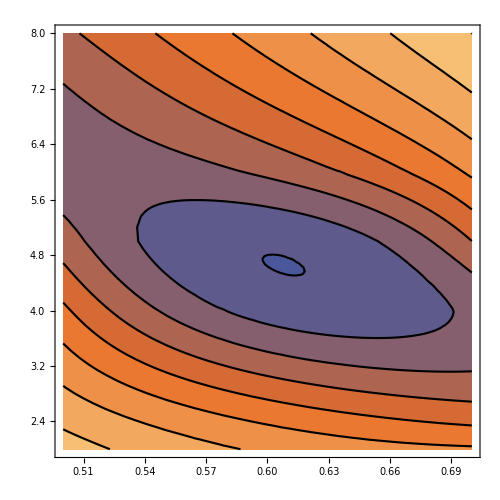

```mathematica
ContourPlot[%190[x,y],{x,0.5,0.7},{y,2.,8.},ContourStyle->Directive[RGBColor[0.,0.,0.],AbsoluteThickness[1.5250000000000001]],PlotTheme->"Scientific",ImageSize->{500,500}]
```

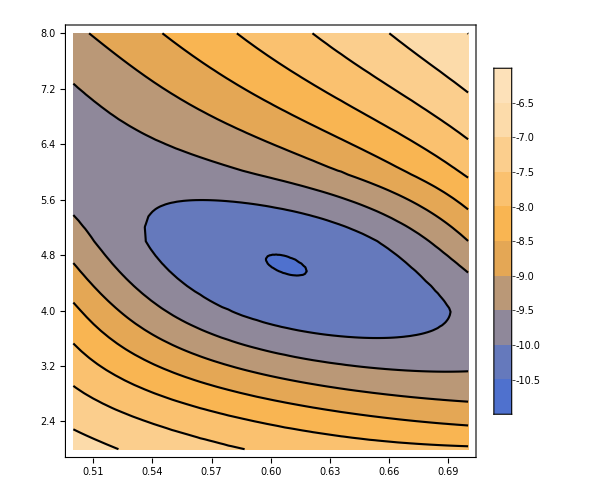

```mathematica
ContourPlot[%190[x,y],{x,0.5,0.7},{y,2.,8.},PlotTheme->"Business",ContourStyle->Directive[RGBColor[0.,0.,0.],AbsoluteThickness[1.5250000000000001]],ImageSize->{500,500}]
```

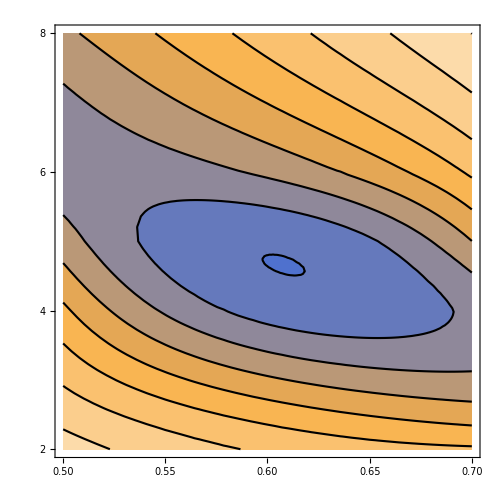

```mathematica
%240[[1]]
```

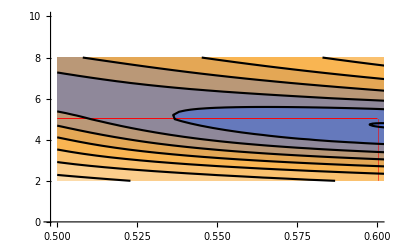

```mathematica
Show[%243,%246]
```

```mathematica
Export["exp.pdf",%240]
```

exp.pdf

```mathematica
SystemOpen["exp.pdf"]
```

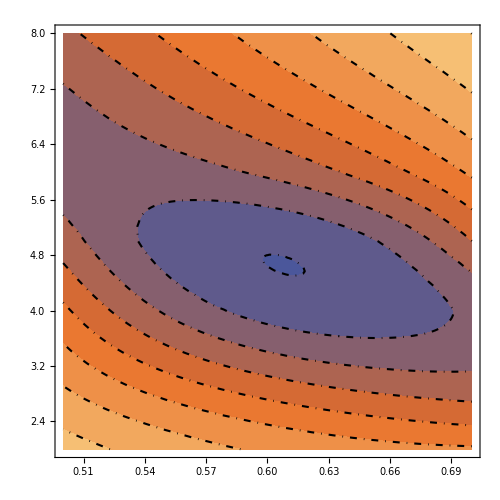

```mathematica
ContourPlot[%190[x,y],{x,0.5,0.7},{y,2.,8.},ContourStyle->Directive[RGBColor[0.,0.,0.],Opacity[1.],AbsoluteThickness[1.5150000000000001],DotDashed],PlotTheme->"Scientific",ImageSize->{500,500}]
```

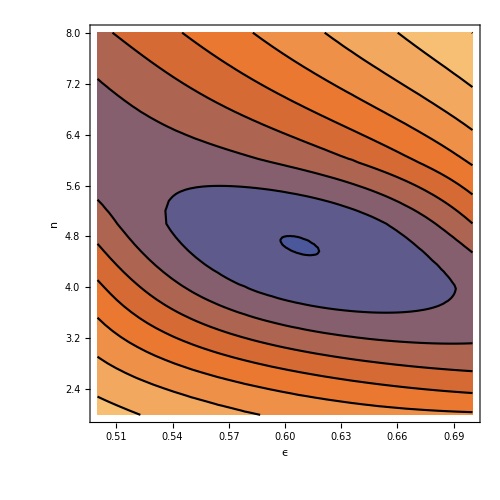

```mathematica
Show[%209,FrameLabel->{{HoldForm[n],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp4,imp7,imp14,imp10,imp7,imp10,imp11,imp14,imp7,imp4,imp11,imp10,imp6,imp10,imp4,imp7,imp13,imp12,imp12,imp11,imp12,imp1,imp3,imp11,imp12,imp1,imp2,imp3,imp4,imp10,imp5,imp10,imp1,imp1,imp2,imp2,imp7,imp9,imp4,imp13,imp6,imp5,imp13,imp13,imp14,imp4,imp5,imp6,imp3,imp5,imp11,imp4,imp6,imp8,imp9,imp8,imp14,imp2,imp8,imp12,imp8,imp2,imp12,imp5,imp9,imp3,imp13,imp8,imp4,imp6,imp9,imp5,imp1,imp14,imp2,imp9,imp11,imp6,imp3,imp10,imp13,imp14,imp12,imp11,imp8,imp7,imp9,imp14,imp8,imp5,imp2,imp9,imp6,imp7,imp3,imp1,imp2,imp3,imp13,imp1}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,4}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,tra1},{ω,Range[0,4,0.01]}];
tra2:=Module[{},
b=Module[{(*imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
*)impa:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1-0.4]]],
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
*)impb:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1-0.4]]],
(*imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
*)impc:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1-0.4]]],
(*imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
*)impd:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1-0.4]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{impa,impb,impc,impd(*,imp7,imp10,imp11,imp14,imp7,imp4,imp11,imp10,imp6,imp10,imp4,imp7,imp13,imp12,imp12,imp11,imp12,imp1,imp3,imp11,imp12,imp1,imp2,imp3,imp4,imp10,imp5,imp10,imp1,imp1,imp2,imp2,imp7,imp9,imp4,imp13,imp6,imp5,imp13,imp13,imp14,imp4,imp5,imp6,imp3,imp5,imp11,imp4,imp6,imp8,imp9,imp8,imp14,imp2,imp8,imp12,imp8,imp2,imp12,imp5,imp9,imp3,imp13,imp8,imp4,imp6,imp9,imp5,imp1,imp14,imp2,imp9,imp11,imp6,imp3,imp10,imp13,imp14,imp12,imp11,imp8,imp7,imp9,imp14,imp8,imp5,imp2,imp9,imp6,imp7,imp3,imp1,imp2,imp3,imp13,imp1*)}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,4}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m52=Table[{ω,tra2},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp3.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list1:={{1,-Log[ρ2]^2},{2,-Log[ρ3]^2},{3,-Log[ρ4]^2},{4,-Log[ρ5]^2},{5,-Log[ρ6]^2},{6,ρ7},{7,ρ8},{8,ρ9},{ρ10},{10,ρ11}};
{(*Min[list1],*)ListLinePlot[m5],list[[Position[list1,Min[list1]][[1,1]],1]],{ρ2,ρ3,ρ4,ρ5,ρ7,ρ8,ρ9,ρ10,ρ11}}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m52[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^4}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list2:={{1+1,-Log[ρ2]^2},{2+1,-Log[ρ3]^2},{3+1,-Log[ρ4]^2},{4+1,-Log[ρ5]^2},{5+1,-Log[ρ6]^2},{6+1,ρ7},{7+1,ρ8},{8+1,ρ9},{9+1,ρ10},{10+1,ρ11}};
{(*Min[list2],*)ListLinePlot[m52,PlotStyle->Red],list[[Position[list2,Min[list2]][[1,1]],1]],ListPlot[{ρ2,ρ3,ρ4,ρ5,ρ7,ρ8,ρ9,ρ10,ρ11}]}];
{(*υ1,*)υ2,μ4,μ7,μ14,μ10}]
```

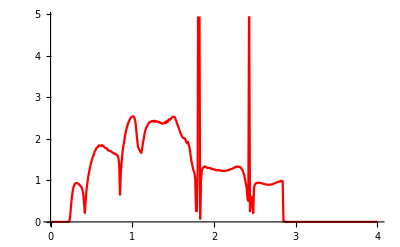
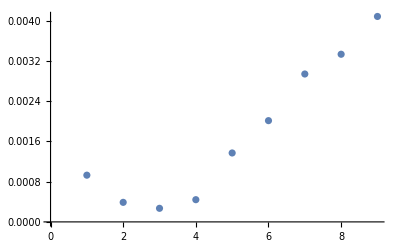
{{-Graphics-,3,-Graphics-},9,10,8,9}

```mathematica
misfit[0.3,1.5,0]
```

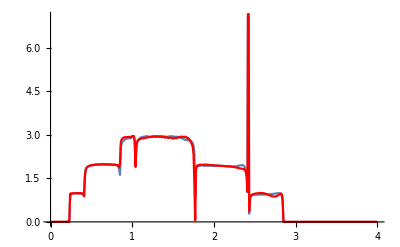

```mathematica
Show[misfit[0.3,1.5,0.0][[1,1]],misfit[0.3,1.5,0.0][[2,1]]]
```

```mathematica
Table[misfit[0.3,1.5,0.0],10]
```

{{{2,{0.000147653,0.000125853,0.000167154,0.000244287,0.000534147,0.000724172,0.000956678,0.00106113,0.00127275}},{1,{0.00106212,0.00204332,0.00314497,0.00438655,0.00700598,0.00834087,0.010094,0.010662,0.0118863}}},{{1,{0.0000254023,0.000027705,0.0000842928,0.000180374,0.000478334,0.00067667,0.000960835,0.000994351,0.00120425}},{1,{0.000878447,0.00189412,0.00302814,0.00430826,0.00699014,0.00835493,0.0101501,0.0107208,0.0119689}}},{{1,{0.0000525558,0.0000910331,0.000162592,0.000267034,0.000532053,0.000714019,0.00101305,0.00097758,0.00116461}},{1,{0.000776318,0.0017519,0.00284521,0.00407896,0.00668019,0.00801063,0.00977454,0.010335,0.0115658}}},{{2,{0.00021557,0.000197893,0.000231923,0.000313156,0.000560571,0.000737662,0.00103708,0.000996561,0.00118299}},{1,{0.000730849,0.00164337,0.0026953,0.00391443,0.00648211,0.00780768,0.00955506,0.0101054,0.0113274}}},{{2,{0.000409981,0.000357789,0.000365318,0.000425749,0.000642527,0.000805993,0.0010904,0.00104623,0.00122268}},{1,{0.000797981,0.00165368,0.00266147,0.00384924,0.00635681,0.00766157,0.00937561,0.0099112,0.0111145}}},{{2,{0.000386787,0.000349799,0.000371204,0.000444568,0.000683651,0.000856757,0.00115253,0.00111331,0.00129814}},{1,{0.000851065,0.00174862,0.00279254,0.00401234,0.0065776,0.00790594,0.00964973,0.0102039,0.0114266}}},{{1,{0.0000168262,0.0000509568,0.000127933,0.000237388,0.000544348,0.000743499,0.00102933,0.00106502,0.0012748}},{1,{0.000942702,0.00197937,0.00312788,0.00440802,0.00710091,0.00846662,0.0102708,0.0108556,0.0121114}}},{{2,{0.000216675,0.00015837,0.000167885,0.00022651,0.000467678,0.000636546,0.000888103,0.000920955,0.00110931}},{1,{0.000835456,0.00174096,0.0027953,0.00401205,0.00658228,0.00790656,0.00963604,0.0101852,0.0113973}}},{{1,{0.0000739302,0.0000842579,0.00015091,0.000252563,0.000572294,0.000776441,0.0010456,0.00112712,0.001347}},{1,{0.00108646,0.00213783,0.00330071,0.00459799,0.00731514,0.00869344,0.010499,0.0110839,0.0123428}}},{{1,{0.0000596464,0.0000666056,0.000130537,0.000230229,0.000545864,0.000749817,0.0010224,0.00109564,0.00131434}},{1,{0.00105143,0.00209689,0.00325467,0.00454965,0.00726015,0.00863729,0.0104415,0.011023,0.0122804}}}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],Table[imp,58]]]
```

{imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp1,imp,imp6,imp12,imp3,imp,imp2,imp,imp,imp,imp,imp,imp,imp8,imp10,imp,imp6,imp2,imp13,imp,imp,imp6,imp4,imp11,imp,imp3,imp,imp,imp14,imp,imp,imp11,imp12,imp8,imp,imp,imp8,imp,imp4,imp,imp,imp1,imp9,imp,imp,imp,imp7,imp10,imp2,imp,imp,imp,imp5,imp,imp,imp,imp1,imp4,imp,imp14,imp,imp,imp,imp,imp5,imp,imp12,imp,imp14,imp,imp,imp11,imp9,imp7,imp13,imp,imp,imp,imp10,imp13,imp,imp,imp7,imp5,imp,imp9,imp,imp,imp,imp}

```mathematica
deltae[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp11,imp5,imp8,imp10,imp9,imp4,imp12,imp14,imp3,imp8,imp5,imp,imp14,imp6,imp10,imp2,imp6,imp12,imp4,imp6,imp2,imp11,imp8,imp1,imp2,imp13,imp5,imp13,imp14,imp3,imp1,imp8,imp3,imp9,imp13,imp4,imp5,imp3,imp1,imp11,imp7,imp2,imp10,imp1,imp13,imp6,imp7,imp13,imp13,imp9,imp3,imp8,imp7,imp1,imp5,imp14,imp7,imp14,imp7,imp14,imp2,imp10,imp1,imp,imp1,imp12,imp3,imp6,imp5,imp11,imp7,imp4,imp11,imp12,imp3,imp8,imp12,imp6,imp9,imp12,imp14,imp11,imp10,imp9,imp5,imp4,imp11,imp8,imp12,imp6,imp13,imp4,imp10,imp2,imp9,imp2,imp4,imp7,imp10,imp9}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
Table[{ω,If[tra>3,3,tra]},{ω,Range[0,3,0.01]}]]
```

```mathematica
aa=Table[deltae[0.5],50]
```

{{{0.,2.14771×10^-8},{0.01,6.76526×10^-6},{0.02,9.10463×10^-7},{0.03,0.0000480895},{0.04,0.0000806464},{0.05,0.000087979},{0.06,0.0000933999},{0.07,0.000044612},{0.08,0.000132916},{0.09,0.000184707},{0.1,0.000726712},{0.11,0.0000416697},{0.12,0.000740557},{0.13,0.000723334},273,{2.87,0.245313},{2.88,0.000102644},{2.89,0.0841},{2.9,0.00158304},{2.91,0.0000200909},{2.92,0.00031836},{2.93,0.000412113},{2.94,0.0000831082},{2.95,0.000115965},{2.96,0.0000225173},{2.97,0.0000913345},{2.98,0.00788186},{2.99,8.13159×10^-6},{3.,0.0000470773}},48,{1}}
 |  |  |  |

```mathematica
pp=Table[Table[{ω,Interpolation[aa[[δ]]][ω]},{ω,0,3,0.001}],{δ,50}]
```

{{{0.,2.14771×10^-8},{0.001,3.13331×10^-6},{0.002,5.52847×10^-6},{0.003,7.27259×10^-6},{0.004,8.43129×10^-6},{0.005,9.07021×10^-6},{0.006,9.25499×10^-6},{0.007,9.05125×10^-6},{0.008,8.52462×10^-6},{0.009,7.74075×10^-6},{0.01,6.76526×10^-6},{0.011,5.66378×10^-6},{0.012,4.50195×10^-6},2975,{2.988,0.00170433},{2.989,0.000828454},{2.99,8.13159×10^-6},{2.991,-0.000733064},{2.992,-0.00137156},{2.993,-0.00188377},{2.994,-0.00224612},{2.995,-0.00243504},{2.996,-0.00242695},{2.997,-0.00219827},{2.998,-0.00172542},{2.999,-0.000984831},{3.,0.0000470773}},48,{{0.,23},3000}}
 |  |  |  |

```mathematica
ns[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,k]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,k]*s[ω,k]+0*Abs[γ[ω,k]]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
anamisfit[lim1_,lim2_,k_,δ_]:=NIntegrate[Interpolation[Table[{ω,(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]])^2},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]+3*NIntegrate[Interpolation[Table[{ω,sa[ω,k]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]^2/(NIntegrate[Interpolation[Table[{ω,(sa[ω,k]*sa[ω,k])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
Table[anamisfit[0.9,1.5,k,12],{k,Range[0,0.8,0.1]}]
```

{7.59334,10.7183,12.9871,14.026,14.414,14.5162,14.531,14.5218,14.5081}

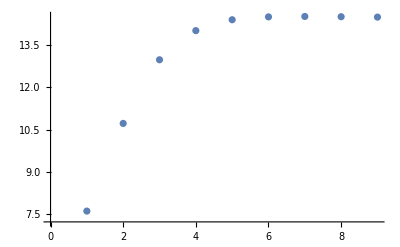

```mathematica
ListPlot[{7.593336626867339,10.71834264709446,12.987091520840501,14.025985740640282,14.413999122342803,14.516162148626629,14.531001431157426,14.521784111698635,14.508148490507486}]
```

```mathematica
nss[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,0]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,0]*s[ω,0]+2*γ[ω,k]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
Table[ns[0.9,1.5,δ,7],{δ,50}]
```

{6.89604,6.96726,6.79484,7.17399,6.9463,6.67951,7.25014,7.04201,6.88344,6.89716,6.96009,7.16496,7.177,7.08692,6.92454,7.12253,6.92871,6.91234,7.11334,7.03193,6.77286,7.17739,6.70627,6.69743,7.1724,6.92911,6.88644,6.68279,6.81294,6.60006,6.98882,6.8859,7.12971,7.27271,6.92115,6.97037,7.17917,6.82324,7.0695,7.12602,6.71912,6.6115,6.97038,7.21848,6.99832,6.873,6.91033,7.04298,7.04563,7.05305}

```mathematica
Around[%294]
```

2.050.06

```mathematica
Around[%304]
```

2.540.10

```mathematica
Around[%312]
```

3.040.10

```mathematica
Around[%319]
```

3.530.10

```mathematica
Around[%326]
```

4.040.13

```mathematica
Around[%334]
```

4.520.15

```mathematica
Around[%341]
```

5.000.14

```mathematica
Around[%348]
```

5.520.15

```mathematica
Around[%358]
```

6.000.16

```mathematica
Around[%366]
```

6.440.17

```mathematica
Around[%373]
```

6.960.17

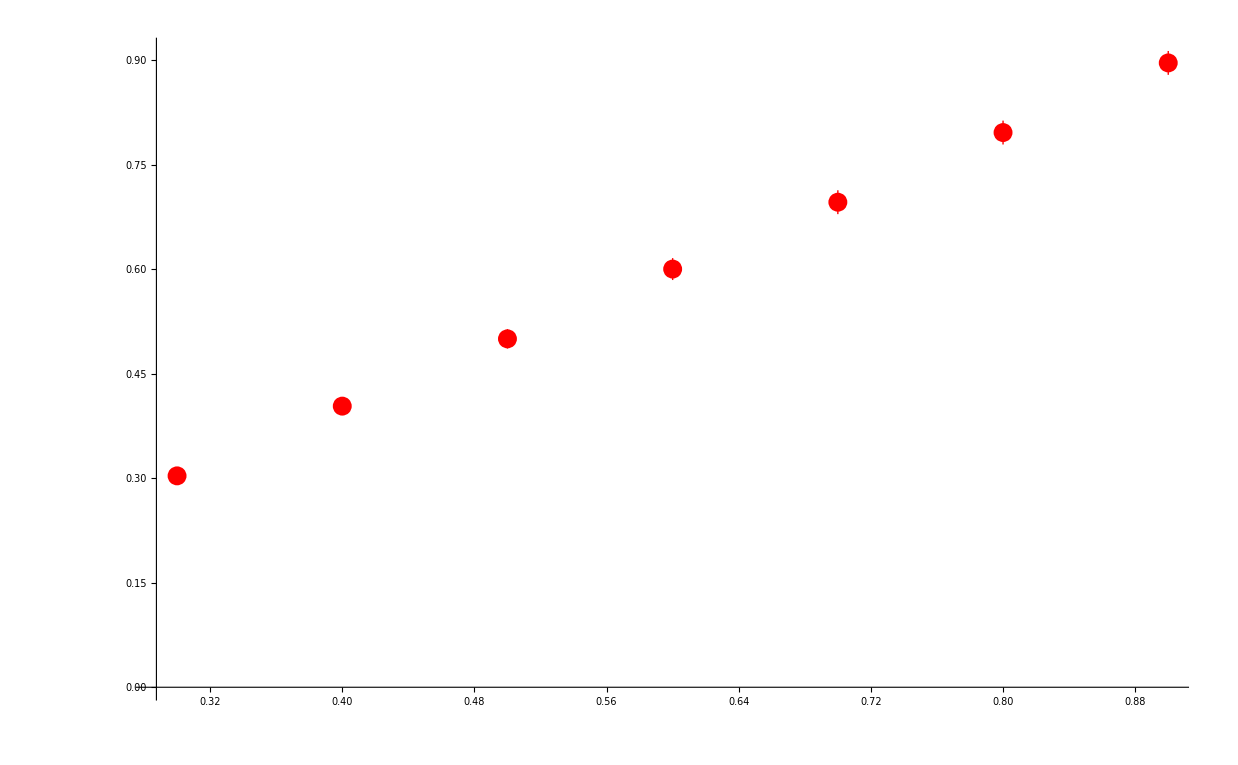

```mathematica
ListPlot[{{0.3,%313/10},{.4,%332/10},{0.5,%342/10},{0.6,%359/10},{0.7,%374/10},{0.8,(%374+1)/10},{0.9,(%374+2)/10}},PlotStyle->Red]
```

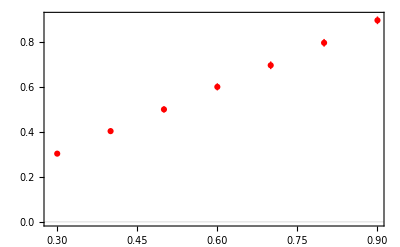

```mathematica
ListPlot[{{0.3,(%313)/10},{0.4,(%332)/10},{0.5,(%342)/10},{0.6,(%359)/10},{0.7,(%374)/10},{0.8,(%374+1)/10},{0.9,(%374+2)/10}},PlotTheme->"Scientific",PlotStyle->RGBColor[1,0,0]]
```

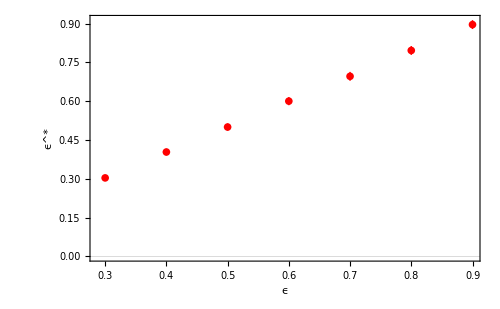

```mathematica
Show[%395,FrameLabel->{{HoldForm[SuperStar[ϵ]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->{500,500}]
```

```mathematica
Table[{x,x},{x,1,7,1}]
```

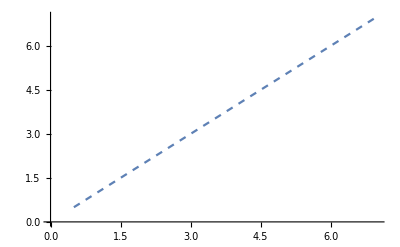

```mathematica
ListLinePlot[{{0.5,0.5},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7}},PlotStyle->Dashed]
```

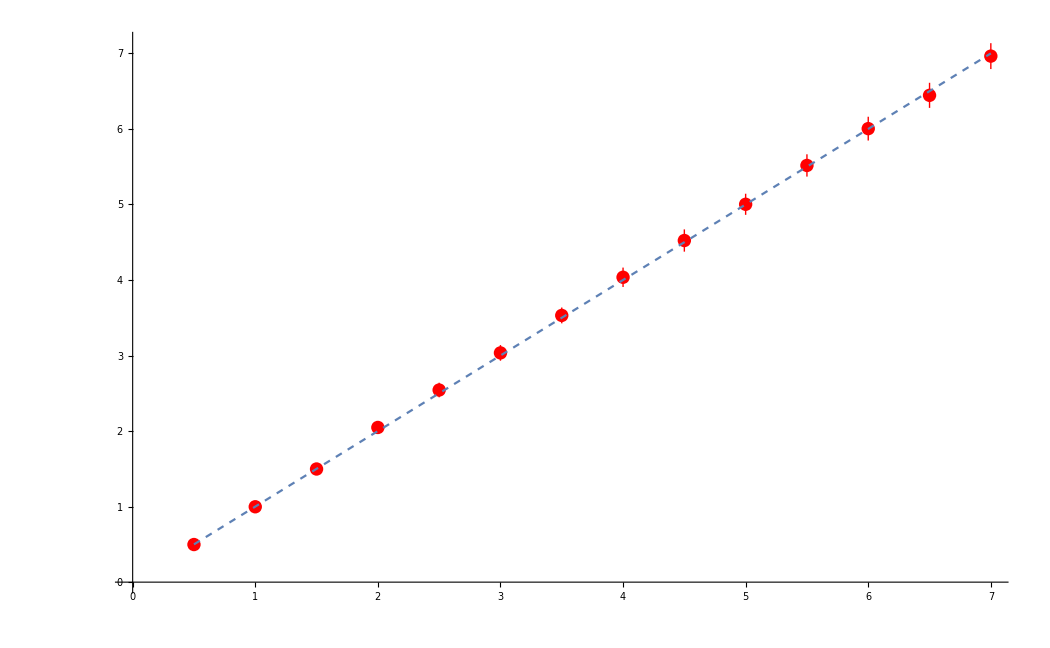

```mathematica
Show[%381,%383]
```

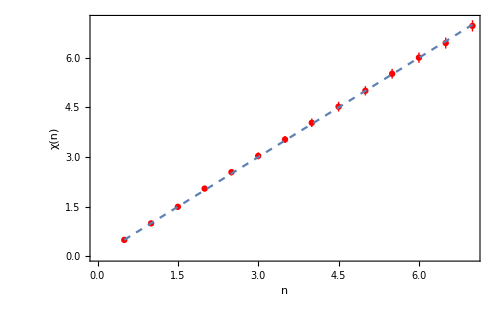

```mathematica
Show[%384,AxesLabel->{HoldForm[n],HoldForm[χ[n]]},PlotLabel->None,LabelStyle->{14,GrayLevel[0]},ImageSize->{500,500},Frame->True]
```

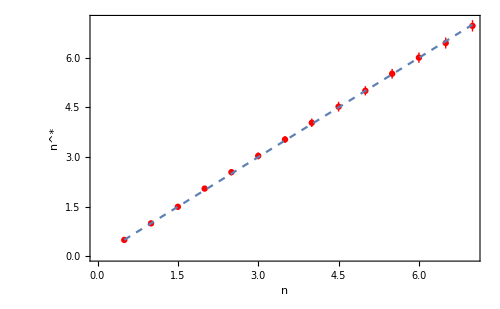

```mathematica
Show[%387,FrameLabel->{{HoldForm[SuperStar[n]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
0.550.04
```

0.550.04

```mathematica
Around[Table[RandomReal[{-0.05,0.1}],100]]
```

0.030.04

```mathematica
Table[nss[0.9,1.5,15,k],{k,Range[0.5,8,0.5]}]
```

{0.454766,0.527905,0.629078,2.16222,0.813298,0.908073,0.876554,0.990492,0.905907,0.870427,0.924358,0.989828,0.942357,0.982347,0.935437,0.861916}

```mathematica
Table[nss[0.9,1.5,δ,2],{δ,50}]
```

{2.32898,2.02325,2.42194,1.9656,2.35989,2.35408,2.31411,2.30986,2.24689,2.32763,2.26874,2.1032,2.00174,2.30652,2.16222,2.43451,2.30869,2.32309,2.38837,2.42999,2.29448,2.36517,2.1848,2.48576,2.20219,2.19249,2.44549,2.36075,2.03228,2.22648,2.21265,2.22209,2.17832,2.3445,2.32608,2.41989,2.37509,2.53581,2.61412,2.2856,2.30275,2.07202,2.34626,2.49562,2.43932,2.5814,2.4091,2.28659,2.32358,2.31219}

```mathematica
Around[%437]
```

2.310.14

```mathematica
Join[{{0.5,%453-0.55}},{{1,%165}},{{1.5,%454}},{{2,%149}},{{2.5,%455}},{{3,%176}},{{3.5,%452-3.5}},{{4,%188}},{{4.5,%452-3.55}},{{5,%198}},{{5.5,%198}},{{6,%208}},{{6.5,%165}},{{7,%219}},{{7.5,%176}},{{8,%231}},{{8.5,%165}},{{9,%244}},{{9.5,%244}},{{10,%254}}]
```

{{0.5,0.000.04},{1,0.000.04},{1.5,-0.0010.030},{2,0.0000.026},{2.5,0.030.04},{3,0.0010.021},{3.5,0.050.10},{4,0.0030.023},{4.5,0.000.10},{5,-0.0030.019},{5.5,-0.0030.019},{6,-0.0020.019},{6.5,0.000.04},{7,-0.0080.020},{7.5,0.0010.021},{8,-0.0040.015},{8.5,0.000.04},{9,-0.0030.017},{9.5,-0.0030.017},{10,0.0000.014}}

```mathematica
ListPlot[%479,PlotRange->{-0.2,0.5},PlotStyle->Directive[Blue,PointSize[0.01],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%480,AxesLabel->{HoldForm[n],HoldForm[SuperStar[n]-n]},PlotLabel->None,LabelStyle->{14,GrayLevel[0]},ImageSize->{500,500},Frame->True]
```

-Graphics-

```mathematica
Show[%482,AxesLabel->{None,None},FrameLabel->{{HoldForm[HoldForm[SuperStar[n]-n]],None},{HoldForm[HoldForm[n]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%480,AxesLabel->{None,None},FrameLabel->{{HoldForm[HoldForm[SuperStar[n]-n]],None},{HoldForm[HoldForm[n]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
ListPlot[Join[{%165},{%149},{%176},{%188},{%198},{%208},{%219},{%231},{%244},{%254}],PlotRange->{-.3,0.3},PlotStyle->Directive[Blue,PointSize[0.01],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Table[Abs[intg2[0.9,1.5,y,10]],{y,100}]
```

{10.1389,9.89306,9.72659,10.141,10.125,10.1164,10.1206,10.208,10.1272,10.0396,9.96185,10.1021,10.0925,10.0882,9.82491,10.4076,10.1003,9.96671,10.203,10.1176,10.1469,10.0877,9.84326,10.113,10.0742,10.0572,10.0195,9.96569,9.93555,9.95,9.95791,9.89454,10.1039,10.0368,10.0291,10.2212,9.90234,9.95859,10.015,10.0392,9.99789,10.0949,9.95086,9.79147,10.0689,9.86753,9.90137,9.95434,10.0693,10.1904,9.83262,10.0215,9.85644,9.95743,10.0026,10.1679,10.0614,9.9072,10.0305,9.98739,9.94964,10.1415,9.93515,10.1637,9.94673,9.91512,10.1323,10.0841,10.0551,10.0488,9.97291,9.8944,9.96022,9.92304,10.066,9.93366,10.1291,10.1511,9.78547,9.89392,9.73114,10.1275,9.94845,9.95403,10.1706,10.0939,9.96166,9.90947,10.1575,9.72997,10.0038,9.71233,9.95041,9.80577,10.0306,9.89962,10.0705,9.93123,9.87445,9.97364}

```mathematica
Around[%137]
```

10.010.12

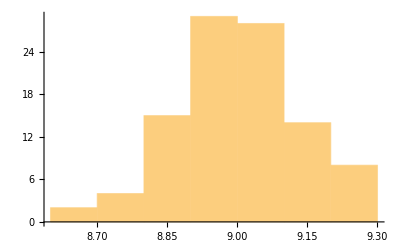

```mathematica
Histogram[%104]
```

```mathematica
Around[%104]
```

9.000.13

```mathematica
Around[%93]
```

8.000.12

```mathematica
ListPlot[Join[{%165},{%149},{%176},{%188},{%198+0.01},{%208+0.015},{%219+0.02},{%231+0.023},{%244+0.027},{%254+0.035}],PlotRange->{-.3,0.3},PlotStyle->Directive[Red,PointSize[0.01],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%272,%273,Frame->True,AxesLabel->{None,HoldForm[SuperStar[n]-n]},FrameLabel->{{HoldForm[Δn/SuperStar[n]],None},{HoldForm[HoldForm[n]],None}},PlotLabel->None,LabelStyle->{18,GrayLevel[0]},ImageSize->{500,500}]
```

-Graphics-

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.0001,1,0,0.5],15000]]},{ω,Range[0,3,0.01]}]
```

{{0.,0.000178906},{0.01,0.000129284},{0.02,0.000113995},{0.03,0.000101099},{0.04,0.000103399},{0.05,0.000112007},{0.06,0.000138354},{0.07,0.000173947},{0.08,0.000229539},{0.09,0.000294689},{0.1,0.000379536},{0.11,0.000481741},{0.12,0.000624354},{0.13,0.000787505},{0.14,0.00100685},{0.15,0.00129503},{0.16,0.00166203},{0.17,0.00211303},{0.18,0.00278217},{0.19,0.00369631},{0.2,0.00499925},{0.21,0.00713594},{0.22,0.0106774},{0.23,0.0202152},{0.24,0.0440542},{0.25,0.0521041},{0.26,0.0694041},{0.27,0.102341},{0.28,0.137796},{0.29,0.180372},{0.3,0.223314},{0.31,0.260769},{0.32,0.286379},{0.33,0.305142},{0.34,0.318827},{0.35,0.330246},{0.36,0.339},{0.37,0.34287},{0.38,0.350652},{0.39,0.352604},{0.4,0.360214},{0.41,0.390294},{0.42,0.505962},{0.43,0.533135},{0.44,0.582527},{0.45,0.741739},{0.46,0.73752},{0.47,0.655389},{0.48,0.574482},{0.49,0.54556},{0.5,0.49789},{0.51,0.469444},{0.52,0.480846},{0.53,0.471479},{0.54,0.476161},{0.55,0.479535},{0.56,0.49303},{0.57,0.49925},{0.58,0.507693},{0.59,0.516191},{0.6,0.536361},{0.61,0.557592},{0.62,0.55769},{0.63,0.57341},{0.64,0.58739},{0.65,0.590901},{0.66,0.612348},{0.67,0.614516},{0.68,0.616698},{0.69,0.63593},{0.7,0.633101},{0.71,0.655302},{0.72,0.649179},{0.73,0.664173},{0.74,0.693569},{0.75,0.675857},{0.76,0.678094},{0.77,0.672194},{0.78,0.700524},{0.79,0.695092},{0.8,0.7131},{0.81,0.685733},{0.82,0.668967},{0.83,0.648494},{0.84,0.61961},{0.85,0.65508},{0.86,0.63324},{0.87,0.677458},{0.88,0.840927},{0.89,0.793754},{0.9,0.759309},{0.91,0.614549},{0.92,0.567387},{0.93,0.531674},{0.94,0.522892},{0.95,0.529305},{0.96,0.540493},{0.97,0.559221},{0.98,0.595271},{0.99,0.616468},{1.,0.650022},{1.01,0.707466},{1.02,0.708276},{1.03,0.577961},{1.04,0.409435},{1.05,0.364389},{1.06,0.35075},{1.07,0.368672},{1.08,0.357051},{1.09,0.34529},{1.1,0.339814},{1.11,0.357301},{1.12,0.357804},{1.13,0.358394},{1.14,0.347369},{1.15,0.350991},{1.16,0.313632},{1.17,0.32781},{1.18,0.323472},{1.19,0.336639},{1.2,0.341645},{1.21,0.350849},{1.22,0.361411},{1.23,0.37051},{1.24,0.373546},{1.25,0.377353},{1.26,0.386861},{1.27,0.387675},{1.28,0.390267},{1.29,0.390489},{1.3,0.393832},{1.31,0.396588},{1.32,0.403157},{1.33,0.415494},{1.34,0.401376},{1.35,0.415019},{1.36,0.415602},{1.37,0.423982},{1.38,0.419013},{1.39,0.410218},{1.4,0.412517},{1.41,0.415128},{1.42,0.408489},{1.43,0.407013},{1.44,0.410871},{1.45,0.395299},{1.46,0.395649},{1.47,0.401092},{1.48,0.394873},{1.49,0.401914},{1.5,0.392124},{1.51,0.392733},{1.52,0.386544},{1.53,0.387936},{1.54,0.382148},{1.55,0.380314},{1.56,0.373366},{1.57,0.378783},{1.58,0.385022},{1.59,0.388377},{1.6,0.39317},{1.61,0.39209},{1.62,0.40517},{1.63,0.396883},{1.64,0.389161},{1.65,0.406269},{1.66,0.448318},{1.67,0.506923},{1.68,0.517081},{1.69,0.505268},{1.7,0.668877},{1.71,0.651722},{1.72,0.888356},{1.73,0.96722},{1.74,1.1387},{1.75,1.66591},{1.76,2.85306},{1.77,7.19149},{1.78,6.5597},{1.79,5.09194},{1.8,3.56142},{1.81,2.98812},{1.82,1.88149},{1.83,1.36283},{1.84,0.816578},{1.85,0.523632},{1.86,0.394449},{1.87,0.334663},{1.88,0.331675},{1.89,0.346528},{1.9,0.362272},{1.91,0.366776},{1.92,0.386112},{1.93,0.400146},{1.94,0.408886},{1.95,0.426415},{1.96,0.428253},{1.97,0.425139},{1.98,0.42606},{1.99,0.437762},{2.,0.445576},{2.01,0.438411},{2.02,0.429421},{2.03,0.429535},{2.04,0.439481},{2.05,0.43775},{2.06,0.44135},{2.07,0.440492},{2.08,0.427197},{2.09,0.423453},{2.1,0.408314},{2.11,0.405073},{2.12,0.416263},{2.13,0.398263},{2.14,0.389771},{2.15,0.38717},{2.16,0.388587},{2.17,0.3854},{2.18,0.376829},{2.19,0.35776},{2.2,0.353919},{2.21,0.350684},{2.22,0.338264},{2.23,0.331675},{2.24,0.329124},{2.25,0.3132},{2.26,0.311508},{2.27,0.301822},{2.28,0.291376},{2.29,0.288645},{2.3,0.287101},{2.31,0.279356},{2.32,0.272126},{2.33,0.270759},{2.34,0.278612},{2.35,0.276438},{2.36,0.297058},{2.37,0.31713},{2.38,0.375901},{2.39,0.464288},{2.4,0.61242},{2.41,1.16566},{2.42,3.90325},{2.43,3.81383},{2.44,2.7091},{2.45,2.23042},{2.46,1.72695},{2.47,1.09262},{2.48,0.700551},{2.49,0.433389},{2.5,0.284251},{2.51,0.210134},{2.52,0.201341},{2.53,0.203354},{2.54,0.220012},{2.55,0.222515},{2.56,0.229743},{2.57,0.231588},{2.58,0.235508},{2.59,0.238605},{2.6,0.238384},{2.61,0.24076},{2.62,0.237534},{2.63,0.234435},{2.64,0.230016},{2.65,0.23262},{2.66,0.226428},{2.67,0.224851},{2.68,0.216581},{2.69,0.212781},{2.7,0.207599},{2.71,0.206579},{2.72,0.196986},{2.73,0.186215},{2.74,0.181731},{2.75,0.175544},{2.76,0.164467},{2.77,0.156956},{2.78,0.153247},{2.79,0.144699},{2.8,0.136352},{2.81,0.128722},{2.82,0.125799},{2.83,0.129397},{2.84,0.151217},{2.85,3.62521},{2.86,4.38739},{2.87,3.82805},{2.88,2.58471},{2.89,2.65819},{2.9,1.25433},{2.91,0.898932},{2.92,0.351545},{2.93,0.0851945},{2.94,0.0234391},{2.95,0.00537923},{2.96,0.00333709},{2.97,0.00241006},{2.98,0.00193168},{2.99,0.00159227},{3.,0.00127298}}

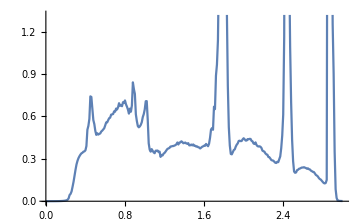

```mathematica
ListPlot[%359,Joined->True]
```

```mathematica
deltae2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp9,imp11,imp8,imp7,imp14,imp,imp6,imp10,imp,imp11,imp6,imp,imp13,imp12,imp,imp,imp5,imp6,imp,imp8,imp1,imp,imp2,imp4,imp,imp10,imp1,imp10,imp4,imp,imp,imp,imp,imp,imp13,imp,imp,imp4,imp,imp5,imp6,imp,imp,imp,imp2,imp13,imp,imp2,imp12,imp,imp,imp,imp,imp9,imp14,imp4,imp,imp5,imp12,imp13,imp,imp,imp,imp14,imp,imp11,imp10,imp,imp8,imp,imp,imp9,imp9,imp11,imp,imp3,imp7,imp,imp7,imp,imp3,imp1,imp8,imp3,imp1,imp,imp,imp12,imp,imp,imp5,imp2,imp3,imp,imp,imp14,imp7}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
tra]
```

```mathematica
RandomSample[{imp,imp,imp,imp9,imp11,imp8,imp7,imp14,imp,imp6,imp10,imp,imp11,imp6,imp,imp13,imp12,imp,imp,imp5,imp6,imp,imp8,imp1,imp,imp2,imp4,imp,imp10,imp1,imp10,imp4,imp,imp,imp,imp,imp,imp13,imp,imp,imp4,imp,imp5,imp6,imp,imp,imp,imp2,imp13,imp,imp2,imp12,imp,imp,imp,imp,imp9,imp14,imp4,imp,imp5,imp12,imp13,imp,imp,imp,imp14,imp,imp11,imp10,imp,imp8,imp,imp,imp9,imp9,imp11,imp,imp3,imp7,imp,imp7,imp,imp3,imp1,imp8,imp3,imp1,imp,imp,imp12,imp,imp,imp5,imp2,imp3,imp,imp,imp14,imp7}]
```

{imp13,imp,imp,imp9,imp8,imp,imp,imp14,imp,imp11,imp,imp14,imp10,imp14,imp,imp6,imp,imp3,imp,imp,imp4,imp,imp,imp,imp,imp,imp1,imp12,imp,imp10,imp,imp7,imp9,imp,imp6,imp5,imp4,imp10,imp2,imp8,imp7,imp1,imp,imp11,imp7,imp,imp,imp5,imp,imp4,imp12,imp11,imp,imp12,imp2,imp13,imp4,imp9,imp3,imp2,imp10,imp3,imp6,imp1,imp,imp,imp13,imp,imp,imp9,imp1,imp,imp,imp11,imp,imp,imp3,imp,imp14,imp6,imp,imp,imp8,imp,imp8,imp,imp5,imp,imp,imp,imp2,imp,imp,imp13,imp5,imp,imp12,imp,imp,imp7}

```mathematica
tra[ω_,ϵ1_]:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},Table[RandomSample[{imp1,imp2,imp3,imp4}],400]]
```

```mathematica
Inverse[tra[0,1][[1]][[2]]]
```

{{-1.+0.0001 ⅈ,-1.-1.17249×10^-20 ⅈ,2.77556×10^-17+2.71051×10^-20 ⅈ,-1.66533×10^-16+1.22358×10^-21 ⅈ,-8.32668×10^-17+1.6263×10^-19 ⅈ,-2.22045×10^-16+1.87335×10^-20 ⅈ,1.66533×10^-16-2.71051×10^-20 ⅈ,2.71051×10^-24+9.81401×10^-20 ⅈ,-4.16333×10^-17-8.13152×10^-20 ⅈ,-4.44089×10^-16-5.72034×10^-20 ⅈ,-8.32667×10^-17+1.35525×10^-20 ⅈ,1.11022×10^-16-3.2838×10^-21 ⅈ,4.16334×10^-17-2.71051×10^-20 ⅈ,-1.-2.63363×10^-20 ⅈ},{-1.-2.20229×10^-20 ⅈ,3.20637×10^-17+0.0001 ⅈ,-1.-8.60306×10^-21 ⅈ,4.82827×10^-17+3.02059×10^-20 ⅈ,-1.66533×10^-16+8.33959×10^-20 ⅈ,-1.90844×10^-17+3.1431×10^-20 ⅈ,1.11022×10^-16-1.01816×10^-19 ⅈ,1.56034×10^-18+4.89463×10^-20 ⅈ,1.66533×10^-16-3.37188×10^-21 ⅈ,-2.59339×10^-17-1.13895×10^-20 ⅈ,5.55111×10^-17+3.77659×10^-20 ⅈ,-6.21165×10^-17-2.46548×10^-20 ⅈ,1.11022×10^-16-9.28295×10^-22 ⅈ,-2.45984×10^-17+2.71051×10^-20 ⅈ},{1.11022×10^-16+1.81081×10^-20 ⅈ,-1.-3.72657×10^-20 ⅈ,6.93889×10^-17+0.0001 ⅈ,-1.+2.37545×10^-20 ⅈ,-2.28983×10^-16+6.1072×10^-20 ⅈ,-1.20829×10^-16+5.68738×10^-20 ⅈ,4.16334×10^-17-5.42101×10^-20 ⅈ,9.80632×10^-18-1.30443×10^-19 ⅈ,-6.93889×10^-18-1.6263×10^-19 ⅈ,-1.20829×10^-16-1.59757×10^-20 ⅈ,-9.71445×10^-17-1.21973×10^-19 ⅈ,-1.-3.62903×10^-20 ⅈ,1.38778×10^-17-4.40885×10^-20 ⅈ,-1.01216×10^-16+7.1751×10^-20 ⅈ},{3.70074×10^-17+9.9069×10^-22 ⅈ,2.05271×10^-17-2.37621×10^-20 ⅈ,-1.-2.0783×10^-20 ⅈ,-1.38644×10^-17+0.0001 ⅈ,-1.+6.28386×10^-21 ⅈ,-5.65761×10^-17-5.29091×10^-20 ⅈ,-5.55112×10^-17+1.04308×10^-19 ⅈ,-1.81639×10^-16-7.5764×10^-20 ⅈ,1.66533×10^-16+3.36207×10^-20 ⅈ,1.75241×10^-16-4.93095×10^-20 ⅈ,5.55111×10^-17+2.5176×10^-20 ⅈ,-1.30727×10^-16-1.12096×10^-19 ⅈ,1.11022×10^-16-2.21449×10^-21 ⅈ,2.36966×10^-16+6.03359×10^-20 ⅈ},{4.85723×10^-17-3.04529×10^-20 ⅈ,1.28416×10^-16-2.82119×10^-20 ⅈ,9.02056×10^-17-3.74055×10^-20 ⅈ,-1.+5.88286×10^-21 ⅈ,-9.71445×10^-17+0.0001 ⅈ,-1.+2.11238×10^-20 ⅈ,1.59595×10^-16-8.13152×10^-20 ⅈ,3.36398×10^-16+2.86158×10^-20 ⅈ,4.85722×10^-17-2.84603×10^-19 ⅈ,-1.-1.04678×10^-19 ⅈ,9.02056×10^-17-8.11338×10^-20 ⅈ,6.39085×10^-16+8.66948×10^-20 ⅈ,-1.38778×10^-17-2.34323×10^-20 ⅈ,-5.78829×10^-16+1.19636×10^-19 ⅈ},{-3.70074×10^-17-3.54128×10^-21 ⅈ,8.67117×10^-18+5.76796×10^-21 ⅈ,2.77556×10^-16-1.06737×10^-20 ⅈ,-2.88206×10^-17-1.10667×10^-21 ⅈ,-1.-8.8188×10^-21 ⅈ,-1.62856×10^-17+0.0001 ⅈ,-1.+1.18731×10^-19 ⅈ,-1.91176×10^-16+6.62038×10^-35 ⅈ,1.11022×10^-16+1.80066×10^-20 ⅈ,1.68803×10^-16-1.11022×10^-20 ⅈ,1.11022×10^-16-4.46876×10^-21 ⅈ,5.50211×10^-17+4.06576×10^-20 ⅈ,1.11022×10^-16-2.88559×10^-21 ⅈ,1.12028×10^-16-2.46548×10^-20 ⅈ},{2.77556×10^-17-1.92835×10^-20 ⅈ,-4.88101×10^-17-3.36984×10^-20 ⅈ,6.93889×10^-18+4.046×10^-21 ⅈ,-2.07615×10^-16-2.48685×10^-20 ⅈ,-4.16334×10^-17+2.44736×10^-20 ⅈ,-1.-3.20307×10^-20 ⅈ,1.31839×10^-16+0.0001 ⅈ,-1.+2.68334×10^-20 ⅈ,6.24501×10^-17-1.32894×10^-19 ⅈ,-2.34342×10^-16-1.17283×10^-20 ⅈ,7.63278×10^-17-6.30226×10^-21 ⅈ,1.65827×10^-16+6.22504×10^-20 ⅈ,6.93891×10^-18-2.38329×10^-20 ⅈ,-3.03772×10^-16+1.47394×10^-19 ⅈ},{-1.66533×10^-16+8.38901×10^-21 ⅈ,1.94539×10^-17+7.35089×10^-21 ⅈ,-5.55112×10^-17+2.73735×10^-20 ⅈ,-1.7685×10^-17+3.38813×10^-20 ⅈ,1.11022×10^-16-1.11146×10^-19 ⅈ,-8.53617×10^-17-6.09864×10^-20 ⅈ,-1.+1.10374×10^-19 ⅈ,-9.71171×10^-17+0.0001 ⅈ,-1.+1.57517×10^-21 ⅈ,1.06821×10^-16-1.0842×10^-19 ⅈ,4.87891×10^-23+1.29411×10^-20 ⅈ,-3.30612×10^-17+2.98156×10^-19 ⅈ,-2.22045×10^-16-3.43341×10^-21 ⅈ,1.0516×10^-16-1.67531×10^-19 ⅈ},{6.9389×10^-18-2.8473×10^-20 ⅈ,-1.24564×10^-16-2.75475×10^-20 ⅈ,2.77556×10^-17+3.93452×10^-20 ⅈ,-1.34547×10^-16-1.07043×10^-20 ⅈ,-2.77556×10^-17-4.61929×10^-20 ⅈ,5.16563×10^-17-2.74113×10^-20 ⅈ,-1.38778×10^-17+2.15851×10^-20 ⅈ,-1.-1.51522×10^-19 ⅈ,2.77556×10^-16+0.0001 ⅈ,-1.-2.73898×10^-21 ⅈ,4.16334×10^-17-2.98727×10^-20 ⅈ,4.23068×10^-17+2.02892×10^-20 ⅈ,-6.93889×10^-18-1.50155×10^-20 ⅈ,-1.20895×10^-16+3.05188×10^-20 ⅈ},{2.22045×10^-16+2.39514×10^-20 ⅈ,1.69379×10^-17-7.35089×10^-21 ⅈ,1.11022×10^-16+3.08919×10^-20 ⅈ,2.11794×10^-17+2.03288×10^-20 ⅈ,-1.-7.07123×10^-20 ⅈ,1.42256×10^-17-2.30393×10^-19 ⅈ,-1.55973×10^-16+1.501×10^-19 ⅈ,-3.31672×10^-16-1.76183×10^-19 ⅈ,-1.-5.53793×10^-20 ⅈ,1.23853×10^-16+0.0001 ⅈ,-1.+1.59269×10^-20 ⅈ,-1.02673×10^-16+2.30393×10^-19 ⅈ,2.22045×10^-16+6.21419×10^-21 ⅈ,1.19611×10^-16-2.25492×10^-19 ⅈ},{-3.38813×10^-25+5.1882×10^-21 ⅈ,-5.08154×10^-17-2.29614×10^-20 ⅈ,6.24501×10^-17-5.12954×10^-20 ⅈ,4.47412×10^-17-5.67604×10^-21 ⅈ,-2.08167×10^-17-2.446×10^-20 ⅈ,9.5393×10^-17-2.96195×10^-20 ⅈ,6.93889×10^-18+7.56472×10^-21 ⅈ,3.70741×10^-16-6.81979×10^-21 ⅈ,3.14004×10^-24-3.14696×10^-20 ⅈ,-1.-3.64207×10^-20 ⅈ,3.46945×10^-17+0.0001 ⅈ,-1.+5.37718×10^-21 ⅈ,-2.08167×10^-17-4.14266×10^-21 ⅈ,-9.40986×10^-17-4.32064×10^-20 ⅈ},{-1.11022×10^-16+2.94117×10^-20 ⅈ,2.55095×10^-18+0. ⅈ,-1.+6.20898×10^-20 ⅈ,1.20873×10^-17+5.42101×10^-20 ⅈ,-2.39132×10^-16-1.56391×10^-19 ⅈ,-7.24923×10^-17-6.77626×10^-20 ⅈ,3.92871×10^-17-2.46262×10^-20 ⅈ,9.16159×10^-17+4.06576×10^-20 ⅈ,-1.55909×10^-16+1.17965×10^-19 ⅈ,5.79364×10^-17+1.35525×10^-20 ⅈ,-1.+6.62745×10^-21 ⅈ,-4.58491×10^-17+0.0001 ⅈ,-1.+1.93626×10^-21 ⅈ,4.84001×10^-17-5.42101×10^-20 ⅈ},{-2.77556×10^-17+5.42101×10^-20 ⅈ,-6.97411×10^-17+1.63474×10^-20 ⅈ,2.77556×10^-17-6.85882×10^-20 ⅈ,-3.03873×10^-17+1.62775×10^-21 ⅈ,2.08167×10^-17-1.64493×10^-20 ⅈ,1.15886×10^-16-1.2724×10^-20 ⅈ,1.38778×10^-17+2.05909×10^-21 ⅈ,3.17181×10^-16+3.36837×10^-20 ⅈ,-2.08167×10^-17-2.07021×10^-20 ⅈ,2.04864×10^-16-3.87395×10^-20 ⅈ,-2.2411×10^-25-1.15549×10^-20 ⅈ,-1.+3.60293×10^-20 ⅈ,-1.38778×10^-17+0.0001 ⅈ,-1.-1.15054×10^-20 ⅈ},{-1.+8.93925×10^-21 ⅈ,-6.81759×10^-17-1.35525×10^-20 ⅈ,1.49344×10^-17+3.86865×10^-20 ⅈ,-7.93596×10^-17-6.77626×10^-21 ⅈ,1.7931×10^-16+3.88499×10^-20 ⅈ,1.6164×10^-16-4.06576×10^-20 ⅈ,1.14934×10^-16-1.17551×10^-19 ⅈ,9.76163×10^-17-1.35525×10^-20 ⅈ,2.07021×10^-16-1.49872×10^-19 ⅈ,-1.58021×10^-16-1.35525×10^-20 ⅈ,-1.99759×10^-17+1.0527×10^-20 ⅈ,7.86616×10^-17-9.48677×10^-20 ⅈ,-1.-4.25726×10^-21 ⅈ,-1.46838×10^-16+0.0001 ⅈ}}

```mathematica
MatrixForm[Chop[%26]]
```

(0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.
-1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | -1.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0 | 0
0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ | -1.
-1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0.+0.0001 ⅈ)

```mathematica
data=Flatten[Table[{x,y,x^2+y^2},{x,-10,10},{y,-10,10}],1]
```

{{-10,-10,200},{-10,-9,181},{-10,-8,164},{-10,-7,149},{-10,-6,136},{-10,-5,125},{-10,-4,116},{-10,-3,109},{-10,-2,104},{-10,-1,101},{-10,0,100},{-10,1,101},{-10,2,104},{-10,3,109},{-10,4,116},{-10,5,125},{-10,6,136},{-10,7,149},{-10,8,164},{-10,9,181},{-10,10,200},{-9,-10,181},{-9,-9,162},{-9,-8,145},{-9,-7,130},{-9,-6,117},{-9,-5,106},{-9,-4,97},{-9,-3,90},{-9,-2,85},{-9,-1,82},{-9,0,81},{-9,1,82},{-9,2,85},{-9,3,90},{-9,4,97},{-9,5,106},{-9,6,117},{-9,7,130},{-9,8,145},{-9,9,162},{-9,10,181},{-8,-10,164},{-8,-9,145},{-8,-8,128},{-8,-7,113},{-8,-6,100},{-8,-5,89},{-8,-4,80},{-8,-3,73},{-8,-2,68},{-8,-1,65},{-8,0,64},{-8,1,65},{-8,2,68},{-8,3,73},{-8,4,80},{-8,5,89},{-8,6,100},{-8,7,113},{-8,8,128},{-8,9,145},{-8,10,164},{-7,-10,149},{-7,-9,130},{-7,-8,113},{-7,-7,98},{-7,-6,85},{-7,-5,74},{-7,-4,65},{-7,-3,58},{-7,-2,53},{-7,-1,50},{-7,0,49},{-7,1,50},{-7,2,53},{-7,3,58},{-7,4,65},{-7,5,74},{-7,6,85},{-7,7,98},{-7,8,113},{-7,9,130},{-7,10,149},{-6,-10,136},{-6,-9,117},{-6,-8,100},{-6,-7,85},{-6,-6,72},{-6,-5,61},{-6,-4,52},{-6,-3,45},{-6,-2,40},{-6,-1,37},{-6,0,36},{-6,1,37},{-6,2,40},{-6,3,45},{-6,4,52},{-6,5,61},{-6,6,72},{-6,7,85},{-6,8,100},{-6,9,117},{-6,10,136},{-5,-10,125},{-5,-9,106},{-5,-8,89},{-5,-7,74},{-5,-6,61},{-5,-5,50},{-5,-4,41},{-5,-3,34},{-5,-2,29},{-5,-1,26},{-5,0,25},{-5,1,26},{-5,2,29},{-5,3,34},{-5,4,41},{-5,5,50},{-5,6,61},{-5,7,74},{-5,8,89},{-5,9,106},{-5,10,125},{-4,-10,116},{-4,-9,97},{-4,-8,80},{-4,-7,65},{-4,-6,52},{-4,-5,41},{-4,-4,32},{-4,-3,25},{-4,-2,20},{-4,-1,17},{-4,0,16},{-4,1,17},{-4,2,20},{-4,3,25},{-4,4,32},{-4,5,41},{-4,6,52},{-4,7,65},{-4,8,80},{-4,9,97},{-4,10,116},{-3,-10,109},{-3,-9,90},{-3,-8,73},{-3,-7,58},{-3,-6,45},{-3,-5,34},{-3,-4,25},{-3,-3,18},{-3,-2,13},{-3,-1,10},{-3,0,9},{-3,1,10},{-3,2,13},{-3,3,18},{-3,4,25},{-3,5,34},{-3,6,45},{-3,7,58},{-3,8,73},{-3,9,90},{-3,10,109},{-2,-10,104},{-2,-9,85},{-2,-8,68},{-2,-7,53},{-2,-6,40},{-2,-5,29},{-2,-4,20},{-2,-3,13},{-2,-2,8},{-2,-1,5},{-2,0,4},{-2,1,5},{-2,2,8},{-2,3,13},{-2,4,20},{-2,5,29},{-2,6,40},{-2,7,53},{-2,8,68},{-2,9,85},{-2,10,104},{-1,-10,101},{-1,-9,82},{-1,-8,65},{-1,-7,50},{-1,-6,37},{-1,-5,26},{-1,-4,17},{-1,-3,10},{-1,-2,5},{-1,-1,2},{-1,0,1},{-1,1,2},{-1,2,5},{-1,3,10},{-1,4,17},{-1,5,26},{-1,6,37},{-1,7,50},{-1,8,65},{-1,9,82},{-1,10,101},{0,-10,100},{0,-9,81},{0,-8,64},{0,-7,49},{0,-6,36},{0,-5,25},{0,-4,16},{0,-3,9},{0,-2,4},{0,-1,1},{0,0,0},{0,1,1},{0,2,4},{0,3,9},{0,4,16},{0,5,25},{0,6,36},{0,7,49},{0,8,64},{0,9,81},{0,10,100},{1,-10,101},{1,-9,82},{1,-8,65},{1,-7,50},{1,-6,37},{1,-5,26},{1,-4,17},{1,-3,10},{1,-2,5},{1,-1,2},{1,0,1},{1,1,2},{1,2,5},{1,3,10},{1,4,17},{1,5,26},{1,6,37},{1,7,50},{1,8,65},{1,9,82},{1,10,101},{2,-10,104},{2,-9,85},{2,-8,68},{2,-7,53},{2,-6,40},{2,-5,29},{2,-4,20},{2,-3,13},{2,-2,8},{2,-1,5},{2,0,4},{2,1,5},{2,2,8},{2,3,13},{2,4,20},{2,5,29},{2,6,40},{2,7,53},{2,8,68},{2,9,85},{2,10,104},{3,-10,109},{3,-9,90},{3,-8,73},{3,-7,58},{3,-6,45},{3,-5,34},{3,-4,25},{3,-3,18},{3,-2,13},{3,-1,10},{3,0,9},{3,1,10},{3,2,13},{3,3,18},{3,4,25},{3,5,34},{3,6,45},{3,7,58},{3,8,73},{3,9,90},{3,10,109},{4,-10,116},{4,-9,97},{4,-8,80},{4,-7,65},{4,-6,52},{4,-5,41},{4,-4,32},{4,-3,25},{4,-2,20},{4,-1,17},{4,0,16},{4,1,17},{4,2,20},{4,3,25},{4,4,32},{4,5,41},{4,6,52},{4,7,65},{4,8,80},{4,9,97},{4,10,116},{5,-10,125},{5,-9,106},{5,-8,89},{5,-7,74},{5,-6,61},{5,-5,50},{5,-4,41},{5,-3,34},{5,-2,29},{5,-1,26},{5,0,25},{5,1,26},{5,2,29},{5,3,34},{5,4,41},{5,5,50},{5,6,61},{5,7,74},{5,8,89},{5,9,106},{5,10,125},{6,-10,136},{6,-9,117},{6,-8,100},{6,-7,85},{6,-6,72},{6,-5,61},{6,-4,52},{6,-3,45},{6,-2,40},{6,-1,37},{6,0,36},{6,1,37},{6,2,40},{6,3,45},{6,4,52},{6,5,61},{6,6,72},{6,7,85},{6,8,100},{6,9,117},{6,10,136},{7,-10,149},{7,-9,130},{7,-8,113},{7,-7,98},{7,-6,85},{7,-5,74},{7,-4,65},{7,-3,58},{7,-2,53},{7,-1,50},{7,0,49},{7,1,50},{7,2,53},{7,3,58},{7,4,65},{7,5,74},{7,6,85},{7,7,98},{7,8,113},{7,9,130},{7,10,149},{8,-10,164},{8,-9,145},{8,-8,128},{8,-7,113},{8,-6,100},{8,-5,89},{8,-4,80},{8,-3,73},{8,-2,68},{8,-1,65},{8,0,64},{8,1,65},{8,2,68},{8,3,73},{8,4,80},{8,5,89},{8,6,100},{8,7,113},{8,8,128},{8,9,145},{8,10,164},{9,-10,181},{9,-9,162},{9,-8,145},{9,-7,130},{9,-6,117},{9,-5,106},{9,-4,97},{9,-3,90},{9,-2,85},{9,-1,82},{9,0,81},{9,1,82},{9,2,85},{9,3,90},{9,4,97},{9,5,106},{9,6,117},{9,7,130},{9,8,145},{9,9,162},{9,10,181},{10,-10,200},{10,-9,181},{10,-8,164},{10,-7,149},{10,-6,136},{10,-5,125},{10,-4,116},{10,-3,109},{10,-2,104},{10,-1,101},{10,0,100},{10,1,101},{10,2,104},{10,3,109},{10,4,116},{10,5,125},{10,6,136},{10,7,149},{10,8,164},{10,9,181},{10,10,200}}

```mathematica
Plot3D[int[x,y],{x,0.3,0.9},{y,-10,10}]
```

-Graphics3D-

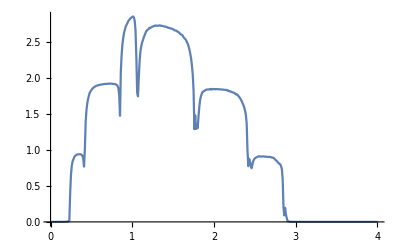

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp5.csv"]]
```

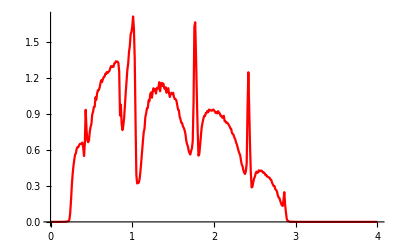

```mathematica
ListLinePlot[Import["/home/shardulmukim//PhD/fwi/7AGNR/100unitcells/42imp100.csv"],PlotStyle->Red]
```

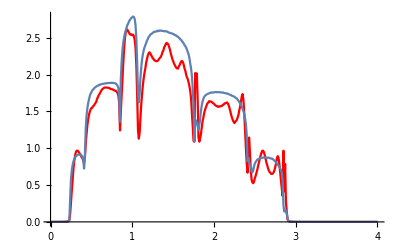

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim//PhD/fwi/7AGNR/8_unit_cells/3imp6.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp6.csv"]],PlotRange->All]
```

```mathematica
Tally[{imp11,imp,imp,imp,imp2,imp8,imp5,imp1,imp,imp,imp,imp10,imp3,imp,imp,imp14,imp6,imp7,imp,imp7,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp8,imp3,imp8,imp,imp,imp,imp1,imp10,imp1,imp12,imp12,imp11,imp,imp,imp13,imp,imp,imp6,imp,imp9,imp,imp2,imp,imp10,imp14,imp,imp,imp,imp9,imp,imp13,imp,imp,imp14,imp,imp6,imp4,imp,imp12,imp,imp,imp,imp,imp5,imp,imp,imp,imp11,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp13,imp9,imp,imp,imp2}]
```

{{imp11,3},{imp,58},{imp2,3},{imp8,3},{imp5,3},{imp1,3},{imp10,3},{imp3,3},{imp14,3},{imp6,3},{imp7,3},{imp4,3},{imp12,3},{imp13,3},{imp9,3}}

```mathematica
misfit[ϵ1_,ϵ2_,y_,x_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp11,imp,imp,imp,imp2,imp8,imp5,imp1,imp,imp,imp,imp10,imp3,imp,imp,imp14,imp6,imp7,imp,imp7,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp8,imp3,imp8,imp,imp,imp,imp1,imp10,imp1,imp12,imp12,imp11,imp,imp,imp13,imp,imp,imp6,imp,imp9,imp,imp2,imp,imp10,imp14,imp,imp,imp,imp9,imp,imp13,imp,imp,imp14,imp,imp6,imp4,imp,imp12,imp,imp,imp,imp,imp5,imp,imp,imp,imp11,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp13,imp9,imp,imp,imp2}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,If[tra1>3,3,tra1]},{ω,Range[0,1.5,0.01]}];v0=Module[{},ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(-m5[[1;;150,2]]+ pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];(*
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];*)
list={{0,0,-Log[ρ2]^2}(*,{4*0.7,4*0.3,-Log[ρ3]^2},{2,2,-Log[ρ4]^2},{4*0.3,4*0.7,-Log[ρ5]^2},{0,4,-Log[ρ6]^2}*)};
list];
v1=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/2/2na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{2,0,-Log[ρ2]^2},{1.4,0.6,-Log[ρ3]^2},{1,1,-Log[ρ4]^2},{0.6,1.4,-Log[ρ5]^2},{0,2,-Log[ρ6]^2}};
list];v2=Module[{},ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/3/na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{3,0,-Log[ρ2]^2},{2.1,0.9,-Log[ρ3]^2},{1.5,1.5,-Log[ρ4]^2},{0.9,2.1,-Log[ρ5]^2},{0,3,-Log[ρ6]^2}};
list];v3=Module[{},ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/4/4na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{4,0,-Log[ρ2]^2},{4*0.7,4*0.3,-Log[ρ3]^2},{2,2,-Log[ρ4]^2},{4*0.3,4*0.7,-Log[ρ5]^2},{0,4,-Log[ρ6]^2}};
list];
v5=Module[{},ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/5/5na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{5,0,-Log[ρ2]^2},{5*0.7,5*0.3,-Log[ρ3]^2},{2.5,2.5,-Log[ρ4]^2},{5*0.3,5*0.7,-Log[ρ5]^2},{0,5,-Log[ρ6]^2}};
list];{v1,v2,v3,v0,v5}]
```

```mathematica
aa=Table[misfit[0.3,0.9,0,1.45],100]
```

{{{{2,0,-42.0342},{1.4,0.6,-43.6527},{1,1,-41.9943},{0.6,1.4,-35.2657},{0,2,-20.4909}},{{3,0,-39.1693},{2.1,0.9,-42.0579},{1.5,1.5,-44.144},{0.9,2.1,-41.9279},{0,3,-23.4909}},{{4,0,-37.3915},{2.8,1.2,-39.7948},{2,2,-42.3289},{1.2,2.8,-44.2312},{0,4,-26.3415}},{{0,0,-13.4236}},{{5,0,-36.2028},{3.5,1.5,-38.0521},{2.5,2.5,-40.5884},{1.5,3.5,-44.1238},{0,5,-29.0014}}},98,{{{2,0,-41.8677},{1.4,0.6,-43.3595},{1,1,-40.7294},{0.6,1.4,-33.4868},{0,2,-19.2194}},3,{{5,0,-33.3451},{3.5,1.5,-35.4281},{2.5,2.5,-38.3472},{1.5,3.5,-41.6805},{0,5,-26.814}}}}
 |  |  |  |

```mathematica
p[x_]:=Join[aa[[x]][[1]],aa[[x]][[2]],aa[[x]][[3]],aa[[x]][[4]],aa[[x]][[5]]]
```

```mathematica
p[1]
```

{{2,0,-42.0342},{1.4,0.6,-43.6527},{1,1,-41.9943},{0.6,1.4,-35.2657},{0,2,-20.4909},{3,0,-39.1693},{2.1,0.9,-42.0579},{1.5,1.5,-44.144},{0.9,2.1,-41.9279},{0,3,-23.4909},{4,0,-37.3915},{2.8,1.2,-39.7948},{2,2,-42.3289},{1.2,2.8,-44.2312},{0,4,-26.3415},{0,0,-13.4236},{5,0,-36.2028},{3.5,1.5,-38.0521},{2.5,2.5,-40.5884},{1.5,3.5,-44.1238},{0,5,-29.0014}}

```mathematica
q[x_]:={Extract[p[x],{{Position[p[x],Min[p[x]]][[1,1]],Position[p[x],Min[p[x]]][[1,2]]-1}}][[1]],Extract[p[x],{{Position[p[x],Min[p[x]]][[1,1]],Position[p[x],Min[p[x]]][[1,2]]-2}}][[1]]}
```

```mathematica
q[1]
```

{2.8,1.2}

```mathematica
Table[q[x],{x,100}]
```

{{2.8,1.2},{3.5,1.5},{3.5,1.5},{1.5,1.5},{2.8,1.2},{0.6,1.4},{0.6,1.4},{1.5,1.5},{0.6,1.4},{0.6,1.4},{2.8,1.2},{3.5,1.5},{2.8,1.2},{0.6,1.4},{0.6,1.4},{3.5,1.5},{0.9,2.1},{0,2},{1,1},{0.6,1.4},{2.8,1.2},{0.6,1.4},{3.5,1.5},{3.5,1.5},{1,1},{0.6,1.4},{3.5,1.5},{3.5,1.5},{1.5,1.5},{1.5,1.5},{0,2},{1.5,1.5},{1.5,1.5},{0.6,1.4},{2.8,1.2},{2.8,1.2},{3.5,1.5},{3.5,1.5},{2.5,2.5},{2.8,1.2},{3.5,1.5},{0.6,1.4},{3.5,1.5},{2.1,0.9},{1.5,1.5},{3.5,1.5},{1,1},{2.8,1.2},{2.8,1.2},{0.6,1.4},{0.6,1.4},{1.5,1.5},{1.5,1.5},{0.6,1.4},{3.5,1.5},{0.6,1.4},{3.5,1.5},{1.5,1.5},{3.5,1.5},{3.5,1.5},{0.6,1.4},{1,1},{1.5,1.5},{3.5,1.5},{3.5,1.5},{0.6,1.4},{2,2},{1,1},{3.5,1.5},{3.5,1.5},{0.6,1.4},{0,2},{0.6,1.4},{1.5,1.5},{1,1},{1,1},{1,1},{2.1,0.9},{0.6,1.4},{1.2,2.8},{3.5,1.5},{2,2},{3.5,1.5},{0.9,2.1},{3.5,1.5},{2.8,1.2},{2,2},{0,2},{2,2},{0.6,1.4},{2,2},{3.5,1.5},{3.5,1.5},{3.5,1.5},{1,1},{3.5,1.5},{0.6,1.4},{0.6,1.4},{2.8,1.2},{0.6,1.4}}

```mathematica
Count[Flatten[%97],.9]
```

12

```mathematica
Extract[p[1],Position[p[1],Min[p[1]]]]
```

{-46.5969}

-42.7085

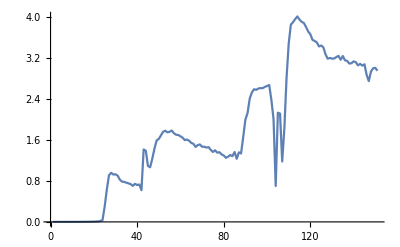

```mathematica
Min[%28]
```

```mathematica
NIntegrate[]
```